# Set DMAX and Directory (RUN FIRST)

EVALUATE THIS CELL FIRST
This notebook is designed such that you construct and save the basis and matrix elements once, for some large value DMAX, then always use those reference files to extract data for any Δmax ≤ DMAX. This cell sets the value of DMAX, which will be used in all later computations, as well as the directory for saving / loading files (by default, it is set to the notebook directory).
By default, we have set DMAX=20, which limits the runtime and resulting file sizes. To accurately reproduce the figures in the paper, the user should set DMAX=40.

```mathematica
DMAX=30;
(*SetDirectory[NotebookDirectory[]];*)
SetDirectory[NotebookDirectory[]]
```

/Users/annamei/Library/CloudStorage/Dropbox/LSZ/Codes for upload

```mathematica
(* These functions help save and load WXF formats *)
binarySave[name_,expr_]:=Export[name<>".WXF",BinarySerialize[expr]];
binaryGet[name_]:=Import[name]//BinaryDeserialize;
```

## Generate Basis

```mathematica
(* Load 'Basis-Scalar.wl' (the scalar basis generation code). *)
Get["Basis-Scalar.wl"];

(* Set the precision to use for orthogonalization *)
precision=50;

(* Compute scalar basis using the function 'computeBosonBasis'. Output is two new variables:
basisBoson = the orthonormalized basis (what we want)
basisBosonPre = pre-orthogonalization (not needed)
Additionally, timing data is printed for each particle number n. *) 
computeBosonBasis[DMAX,precision];

(* Save 'basisBoson' *)
binarySave["BasisBosonD"<>ToString[DMAX],N[basisBoson]];
```

t=0.00003

n@ 1

t=0.00104

n@ 2

t=0.03401

n@ 3

t=0.13115

n@ 4

t=0.414086

n@ 5

t=0.892375

n@ 6

t=1.54534

n@ 7

t=2.23032

n@ 8

t=2.82611

n@ 9

t=3.29527

n@ 10

t=3.632452

n@ 11

t=3.8553

n@ 12

t=4.018499

n@ 13

t=4.133962

n@ 14

t=4.20834

n@ 15

t=4.260027

n@ 16

t=4.290503

n@ 17

t=4.313354

n@ 18

t=4.33089

n@ 19

t=4.344092

n@ 20

t=4.355363

n@ 21

t=4.362985

n@ 22

t=4.368929

n@ 23

t=4.373378

n@ 24

t=4.376665

n@ 25

t=4.379721

n@ 26

t=4.382411

n@ 27

t=4.383977

n@ 28

t=4.385013

n@ 29

t=4.385664

n@ 30

t=4.386017

## Generate Hamiltonian Matrix Elements

```mathematica
(* Load 'MatrixElements-Scalar.wl' (the scalar matrix element generation code). *)
Get["MatrixElements-Scalar.wl"];

(* Load basis file for given Δmax (see 'Generate Basis' section of this notebook) *)
basisBoson=binaryGet["BasisBosonD"<>ToString[DMAX]<>".WXF"];

(* Use the functions in 'MatrixElements-Scalar.wl' to compute Hamiltonian matrices: *)

(* Generate mass matrix. Output is the variable 'fullMassMatrix'. Timing data printed for each particle number n. *)
ComputeScalarMassMatrix[DMAX,basisBoson] ;

(* Generate ϕ^4 (n->n) matrix. Output is the variable 'fullPhi4NtoNMatrix'. Timing data printed for each particle number n. *)
ComputePhi4NtoNMatrix[DMAX,basisBoson]

(* Generate ϕ^4 (n->n+2) matrix. Output is the variable 'fullPhi4NtoNPlus2Matrix'. Timing data printed for each particle number n. *)
ComputePhi4NtoNPlus2Matrix[DMAX,basisBoson]

(* Save output *)
binarySave["ScalarMassD"<>ToString[DMAX],fullMassMatrix];
binarySave["ScalarPhi4NtoND"<>ToString[DMAX],fullPhi4NtoNMatrix];
binarySave["ScalarPhi4NtoN2D"<>ToString[DMAX],fullPhi4NtoNPlus2Matrix];
```

t=0.000067

@ n=1

t=0.00924

@ n=2

t=0.080785

@ n=3

t=0.3375

@ n=4

t=0.863703

@ n=5

t=1.70191

@ n=6

t=2.76382

@ n=7

t=3.89029

@ n=8

t=4.940591

@ n=9

t=5.805448

@ n=10

t=6.487887

@ n=11

t=6.9924

@ n=12

t=7.361084

@ n=13

t=7.624521

@ n=14

t=7.814571

@ n=15

t=7.947762

@ n=16

t=8.040747

@ n=17

t=8.105714

@ n=18

t=8.151155

@ n=19

t=8.183156

@ n=20

t=8.204505

@ n=21

t=8.218639

@ n=22

t=8.227937

@ n=23

t=8.233446

@ n=24

t=8.237664

@ n=25

t=8.239989

@ n=26

t=8.241214

@ n=27

t=8.241882

@ n=28

t=8.242259

@ n=29

t=8.242465

@ n=30

t=0.000043

@ n=2

t=0.18634

@ n=3

t=1.28022

@ n=4

t=4.065468

@ n=5

t=8.518346

@ n=6

t=13.744

@ n=7

t=18.90294

@ n=8

t=23.38256

@ n=9

t=26.9914

@ n=10

t=29.58007

@ n=11

t=31.47419

@ n=12

t=32.74368

@ n=13

t=33.57609

@ n=14

t=34.15582

@ n=15

t=34.51693

@ n=16

t=34.7534

@ n=17

t=34.90537

@ n=18

t=35.00273

@ n=19

t=35.06316

@ n=20

t=35.10033

@ n=21

t=35.12266

@ n=22

t=35.13531

@ n=23

t=35.14285

@ n=24

t=35.14676

@ n=25

t=35.14875

@ n=26

t=35.14979

@ n=27

t=35.15031

@ n=28

t=35.1506

@ n=29

t=35.15075

@ n=30

t=0.000055

@ n=3

t=0.094674

@ n=4

t=0.620044

@ n=5

t=2.04711

@ n=6

t=4.569089

@ n=7

t=8.154217

@ n=8

t=12.38884

@ n=9

t=16.55573

@ n=10

t=20.09428

@ n=11

t=22.79683

@ n=12

t=24.70678

@ n=13

t=25.98131

@ n=14

t=26.79683

@ n=15

t=27.308

@ n=16

t=27.6289

@ n=17

t=27.82875

@ n=18

t=27.95302

@ n=19

t=28.02804

@ n=20

t=28.07381

@ n=21

t=28.10264

@ n=22

t=28.12052

@ n=23

t=28.13044

@ n=24

t=28.13599

@ n=25

t=28.13985

@ n=26

t=28.14174

@ n=27

t=28.14271

@ n=28

t=28.14325

@ n=29

t=28.14356

@ n=30

# Jacobi

### Define Useful Functions

#### Jacobi Polynomials

```mathematica
μNorm[l_,α_,β_]:=√((Gamma[l+1]Gamma[l+α+β+1]Gamma[2l+α+β+2])/(Gamma[l+α+1]Gamma[l+β+1]Gamma[2l+α+β+1]))
```

```mathematica
JacobiMultiParticle[l_List,β_List,p_List]:=Block[
{n=Length[p],α},
Total[p]^l⟦n⟧Product[
α=2Sum[l⟦j⟧,{j,i-1}]+Sum[β⟦j⟧,{j,i}]+i-1;
(Sum[p[[j]],{j,i+1}]^l⟦i⟧)μNorm[l⟦i⟧,α,β⟦i+1⟧] JacobiP[
l⟦i⟧,α,β⟦i+1⟧,(p[[i+1]]-Sum[p[[j]],{j,i}])/(p[[i+1]]+Sum[p[[j]],{j,i}])
],
{i,1,n-1}
]
]//PowerExpand//Simplify
```

#### Scalar Contractions

```mathematica
phiContraction[nl_,nr_,nm_]:=Block[
{dn,
left,mid,right,midSeparation,
midR,midL,contractions,sorted,
factor,rules,measure,
contractedRightMomenta,
freeRightMomenta,
xlLast,xrLast,
allContractions
},
dn=nr-nl;
allContractions=Which[
(* Rule out impossible contractions: *)
(* If (nm-dn) is odd, then there will be a ϕ that cannot be paired; *)
OddQ[nm-dn],Print["impossible"];{},
(* If nm<Abs[dn] then there will be an external |p> or <p| that cannot be paired   *)
nm<Abs[dn],Print["impossible"];{},
True,
(* list of momenta in bra state *)
left=xl/@Range[nl];
(* list of momenta in middle operator *)
mid=xm/@Range[nm];
(* list of momenta in ket state *)
right=xr/@Range[nr];

(* Next we separate the middle operators into the group that acts as annihilation operators and the group that acts as creation operator, as outlined in (1.24).
Then we join the list of annihilation operators with the list of bra state momenta, find all its permutations \vec{j} as, and join the list of creation operators with the list of ket state momenta and get \vec{j'}. For each permutation, we compute the product of one-particle contraction as outlined in (1.25). *)

(* Find all possible way to pick up nc === (nm+dn)/2 middle operators *)
midSeparation={#,Complement[mid,#]}&/@Subsets[mid,{(nm+dn)/2}];
contractions=Flatten[Table[
(* For each separation in midSeparation, identify the two groups of middle operators as {midL,midR} *)
{midL,midR}=thiMidSeparation;
(* The operators in midL act as annihilation operators, we can merge them into the bra state, and generate all permutations, \vec{j}, of the big list. 
The operators in midR act as creation operators, we can merge them into the ket state, and get \vec{j}.
Return the list of all possible permutations, for each permutation, return { \vec{j},\vec{j'} } *)
Table[
Thread[
{permL,
Join[right,midR]}
],{permL,Permutations[Join[left,midL]]}],
{thiMidSeparation,midSeparation}],1];
(* The middle operators are normal ordered, which means contractions like xm[_]->xm[_] is zero, so the permutations that contain such contractions are discarded. *)
contractions=Select[contractions,FreeQ[#,{xm[_],xm[_]}]&];
Table[
(* Take one-particle contractions *)
{factor,rules}=Reap[Times@@Table[
sorted=Sort[pair];
Switch[
sorted,
(* The case in (1.22) *)
{xl[_],xr[_]},Sow[sorted[[2]]->sorted[[1]] ];(2 sorted[[1]])(2π),
(* The case in (1.19) *)
{xl[_],xm[_]},Sow[sorted[[2]]->-sorted[[1]] ];1,
(* The case in (1.18) *)
{xm[_],xr[_]},Sow[sorted[[1]]->sorted[[2]] ];1
],
{pair,contraction}]];
(* Gather all momentum identification from delta function *)
rules=Flatten[rules,1];
(* find all right momenta that are fixed. *)
contractedRightMomenta=Cases[Keys[rules],xr[_]];
(* find all right momenta that are not fixed. *)
freeRightMomenta=Complement[right,contractedRightMomenta];
(* All bra state momenta are not fixed and momenta in freeRightMomenta are not fixed, and they become the integral measure (not taking into account that the total momenta is fixed. *)
measure=Join[left,freeRightMomenta];
{factor,measure,rules},
{contraction,contractions}]
];
(* Gather similar terms *)
{Plus@@#[[;;,1]],#[[1,2]],#[[1,3]]}&/@GatherBy[allContractions,#[[{2,3}]]&]
];
```

#### Scalar inner product

```mathematica
ClearAll[phiInnerProduct];
phiInnerProduct[lLeft_,lRight_]:=Block[{
fockContraction,i=0,
left,right,nl,fL,fR,
res,rules,xlLast,measure,integrand
},
nl=Length[lLeft];
(* list of momenta in bra state *)
left=xl/@Range[nl];
(* list of momenta in ket state *)
right=xr/@Range[nl];
(* The wave funnctions of the external states. *)
fL=JacobiMultiParticle[lLeft,ConstantArray[1,nl],left];
fR=JacobiMultiParticle[lRight,ConstantArray[1,nl],right];
(* The Fock state contraction *)
fockContraction=phiContraction[nl,nl,0];
Sum[(* run through each term in fockContraction *)
i++;(* This index is for Monitor[] *)
 (* momentum identification from delta function  *)
rules=term[[3]];

(* These lines address the delta function of the total momentum of the bra state *)
(* We choose to fix the last left momentum *)
xlLast=left[[-1]];
rules=rules/.(xlLast->1-Total[Drop[left,-1]]);
AppendTo[rules,xlLast->1-Total[Drop[left,-1]]];
(* the list of dxl in the final integral measure  *)
measure=Drop[left,-1];
integrand=term[[1]]*fL*fR/.rules;
res=If[measure=={},integrand,
Integrate[
integrand,
(* The integral measure and the bounds *)
(* the bounds of xl, {xl[1],0,1}, {xl[2],0,1-xl[1]} and so on.. *)
Sequence@@(FoldPairList[
{{#2,0,#1},#1-#2}&,1,
measure
]//Evaluate)]
];
res,
{term,fockContraction}
]
];
```

#### scalar mass

```mathematica
ClearAll[phiMass];
phiMass[lLeft_,lRight_]:=Block[{
fockContraction,i=0,
left,right,nl,fL,fR,
contractedRightMomenta,freeRightMomenta,xrLast,
res,rules,xlLast,measureR,measureL,integrand
},
nl=Length[lLeft];
(* list of momenta in bra state *)
left=xl/@Range[nl];
(* list of momenta in ket state *)
right=xr/@Range[nl];
(* The wave funnctions of the external states. *)
fL=JacobiMultiParticle[lLeft,ConstantArray[1,nl],left];
fR=JacobiMultiParticle[lRight,ConstantArray[1,nl],right];
(* The Fock state contraction *)
fockContraction=phiContraction[nl,nl,2];
Sum[(* run through each term in fockContraction *)
i++;(* This index is for Monitor[] *)
rules=term[[3]]; (* momentum identification from delta function  *)
(* right momenta that are fixed *)
contractedRightMomenta=Cases[Keys[rules],xr[_]];
(* right momenta that are not fixed *)
freeRightMomenta=Complement[right,contractedRightMomenta];

(* These lines address the delta function of the total momentum of the ket state *)
(* We choose to fix the last right momentum that is not fixed *)
xrLast=freeRightMomenta[[-1]];
AppendTo[rules,
xrLast->1-(Total[DeleteCases[right,xrLast]]/.rules)
];
(* measureR is the list of dxr in the final integral measure  *)
measureR=Drop[freeRightMomenta,-1];
freeRightMomenta=Drop[freeRightMomenta,-1];

(* These lines address the delta function of the total momentum of the bra state *)
(* We choose to fix the last left momentum *)
xlLast=left[[-1]];
rules=rules/.(xlLast->1-Total[Drop[left,-1]]);
AppendTo[rules,xlLast->1-Total[Drop[left,-1]]];
(* measureL is the list of dxl in the final integral measure  *)
measureL=Drop[left,-1];

integrand=term[[1]]*fL*fR/.rules;
res=If[(*If there is no integral measrue, then everything is fixed by delta functions. *)
Join[measureL,measureR]=={},integrand,
Integrate[
integrand,
(* The integral measure and the bounds *)
Sequence@@(Join[
(* the bounds of xl, {xl[1],0,1}, {xl[2],0,1-xl[1]} and so on.. *)
FoldPairList[
{{#2,0,#1},#1-#2}&,1,
measureL
],
(* The bounds of xr. Because some of the momenta are fixed already, (1-Total[contractedRightMomenta/.rules]) is the bound on the first integral variable. *)
FoldPairList[
{{#2,0,#1},#1-#2}&,1-Total[contractedRightMomenta/.rules],
measureR
]
]//Evaluate)]
];
res,
{term,fockContraction}
]
];
```

#### scalar quartic

```mathematica
ClearAll[phi4];
phi4[lLeft_,lRight_]:=Block[{
fockContraction,i=0,
left,right,nl,nr,nm=4,fL,fR,
contractedRightMomenta,freeRightMomenta,xrLast,
res,rules,xlLast,measureR,measureL,integrand
},
nl=Length[lLeft];
nr=Length[lRight];
(* list of momenta in bra state *)
left=xl/@Range[nl];
(* list of momenta in ket state *)
right=xr/@Range[nr];
(* The wave funnctions of the external states. *)
fL=JacobiMultiParticle[lLeft,ConstantArray[1,nl],left];
fR=JacobiMultiParticle[lRight,ConstantArray[1,nr],right];
(* The Fock state contraction *)
fockContraction=phiContraction[nl,nr,nm];
Sum[(* run through each term in fockContraction *)
i++;(* This index is for Monitor[] *)
 (* momentum identification from delta function  *)
rules=term[[3]];
(* right momenta that are fixed *)
contractedRightMomenta=Cases[Keys[rules],xr[_]];
(* right momenta that are not fixed *)
freeRightMomenta=Complement[right,contractedRightMomenta];

(* These lines address the delta function of the total momentum of the ket state *)
(* We choose to fix the last right momentum that is not fixed *)
xrLast=freeRightMomenta[[-1]];
AppendTo[rules,
xrLast->1-(Total[DeleteCases[right,xrLast]]/.rules)
];
(* measureR is the list of dxr in the final integral measure  *)
measureR=Drop[freeRightMomenta,-1];
freeRightMomenta=Drop[freeRightMomenta,-1];

(* These lines address the delta function of the total momentum of the bra state *)
(* We choose to fix the last left momentum *)
xlLast=left[[-1]];
rules=rules/.(xlLast->1-Total[Drop[left,-1]]);
AppendTo[rules,xlLast->1-Total[Drop[left,-1]]];
(* measureL is the list of dxl in the final integral measure  *)
measureL=Drop[left,-1];
integrand=term[[1]]*fL*fR/.rules;
res=If[(*If there is no integral measrue, then everything is fixed by delta functions. *)
Join[measureL,measureR]=={},integrand,
Integrate[
integrand,
(* The integral measure and the bounds *)
Sequence@@(Join[
(* the bounds of xl, {xl[1],0,1}, {xl[2],0,1-xl[1]} and so on.. *)
FoldPairList[
{{#2,0,#1},#1-#2}&,1,
measureL
],
(* The bounds of xr. Because some of the momenta are fixed already, (1-Total[contractedRightMomenta/.rules]) is the bound on the first integral variable. *)
FoldPairList[
{{#2,0,#1},#1-#2}&,1-Total[contractedRightMomenta/.rules],
measureR
]
]//Evaluate)] ];
res,
{term,fockContraction}
]
];
```

#### ϕ^3 form factor

```mathematica
ClearAll[phi3FF];
phi3FF[lLeft_,lRight_]:=Block[{
fockContraction,i=0,
left,right,nl,nr,nm=3,fL,fR,
contractedRightMomenta,freeRightMomenta,xrLast,
res,rules,xlLast,measureR,measureL,integrand
},
nl=Length[lLeft];
nr=Length[lRight];
(* list of momenta in bra state *)
left=xl/@Range[nl];
(* list of momenta in ket state *)
right=xr/@Range[nr];
(* The wave funnctions of the external states. *)
fL=JacobiMultiParticle[lLeft,ConstantArray[1,nl],left];
fR=JacobiMultiParticle[lRight,ConstantArray[1,nr],right];
(* The Fock state contraction *)
fockContraction=phiContraction[nl,nr,nm];
Sum[(* run through each term in fockContraction *)
i++;(* This index is for Monitor[] *)
 (* momentum identification from delta function  *)
rules=term[[3]];
(* right momenta that are fixed *)
contractedRightMomenta=Cases[Keys[rules],xr[_]];
(* right momenta that are not fixed *)
freeRightMomenta=Complement[right,contractedRightMomenta];

(* These lines address the delta function of the total momentum of the ket state *)
(* We choose to fix the last right momentum that is not fixed *)
xrLast=freeRightMomenta[[-1]];
AppendTo[rules,
xrLast->1-(Total[DeleteCases[right,xrLast]]/.rules)
];
(* measureR is the list of dxr in the final integral measure  *)
measureR=Drop[freeRightMomenta,-1];
freeRightMomenta=Drop[freeRightMomenta,-1];

(* These lines address the delta function of the total momentum of the bra state *)
(* We choose to fix the last left momentum *)
xlLast=left[[-1]];
rules=rules/.(xlLast->p1-Total[Drop[left,-1]]);
AppendTo[rules,xlLast->p1-Total[Drop[left,-1]]];
(* measureL is the list of dxl in the final integral measure  *)
measureL=Drop[left,-1];
integrand=term[[1]]*fL*fR/.rules;
res=If[(*If there is no integral measrue, then everything is fixed by delta functions. *)
Join[measureL,measureR]=={},integrand,
Integrate[
integrand,
(* The integral measure and the bounds *)
Sequence@@(Join[
(* the bounds of xl, {xl[1],0,1}, {xl[2],0,1-xl[1]} and so on.. *)
FoldPairList[
{{#2,0,#1},#1-#2}&,p1,
measureL
],
(* The bounds of xr. Because some of the momenta are fixed already, (1-Total[contractedRightMomenta/.rules]) is the bound on the first integral variable. *)
FoldPairList[
{{#2,0,#1},#1-#2}&,1-Total[contractedRightMomenta/.rules],
measureR
]
]//Evaluate)] ];
res,
{term,fockContraction}
]
];
```

#### ϕ form factor

```mathematica
ClearAll[phiFF];
phiFF[lLeft_,lRight_]:=Block[{
fockContraction,i=0,
left,right,nl,nr,nm=1,fL,fR,
contractedRightMomenta,freeRightMomenta,xrLast,
res,rules,xlLast,measureR,measureL,integrand
},
nl=Length[lLeft];
nr=Length[lRight];
(* list of momenta in bra state *)
left=xl/@Range[nl];
(* list of momenta in ket state *)
right=xr/@Range[nr];
(* The wave funnctions of the external states. *)
fL=JacobiMultiParticle[lLeft,ConstantArray[1,nl],left];
fR=JacobiMultiParticle[lRight,ConstantArray[1,nr],right];
(* The Fock state contraction *)
fockContraction=phiContraction[nl,nr,nm];
Sum[(* run through each term in fockContraction *)
i++;(* This index is for Monitor[] *)
 (* momentum identification from delta function  *)
rules=term[[3]];
(* right momenta that are fixed *)
contractedRightMomenta=Cases[Keys[rules],xr[_]];
(* right momenta that are not fixed *)
freeRightMomenta=Complement[right,contractedRightMomenta];

(* These lines address the delta function of the total momentum of the ket state *)
(* We choose to fix the last right momentum that is not fixed *)
xrLast=freeRightMomenta[[-1]];
AppendTo[rules,
xrLast->1-(Total[DeleteCases[right,xrLast]]/.rules)
];
(* measureR is the list of dxr in the final integral measure  *)
measureR=Drop[freeRightMomenta,-1];
freeRightMomenta=Drop[freeRightMomenta,-1];

(* These lines address the delta function of the total momentum of the bra state *)
(* We choose to fix the last left momentum *)
xlLast=left[[-1]];
rules=rules/.(xlLast->p1-Total[Drop[left,-1]]);
AppendTo[rules,xlLast->p1-Total[Drop[left,-1]]];
(* measureL is the list of dxl in the final integral measure  *)
measureL=Drop[left,-1];
integrand=term[[1]]*fL*fR/.rules;
res=If[(*If there is no integral measrue, then everything is fixed by delta functions. *)
Join[measureL,measureR]=={},integrand,
Integrate[
integrand,
(* The integral measure and the bounds *)
Sequence@@(Join[
(* the bounds of xl, {xl[1],0,1}, {xl[2],0,1-xl[1]} and so on.. *)
FoldPairList[
{{#2,0,#1},#1-#2}&,p1,
measureL
],
(* The bounds of xr. Because some of the momenta are fixed already, (1-Total[contractedRightMomenta/.rules]) is the bound on the first integral variable. *)
FoldPairList[
{{#2,0,#1},#1-#2}&,1-Total[contractedRightMomenta/.rules],
measureR
]
]//Evaluate)] ];
res,
{term,fockContraction}
]
];
```

### Generate ϕ and ϕ^3 matrices to compare with Radial Quantization results

```mathematica
JacobiStates={{0},{0,0},{2,0},{4,0},{6,0},{8,0},{0,0,0},{2,0,0},{2,1,0},{0,0,0,0},{2,0,0,0},{2,1,0,0}}
```

{{0},{0,0},{2,0},{4,0},{6,0},{8,0},{0,0,0},{2,0,0},{2,1,0},{0,0,0,0},{2,0,0,0},{2,1,0,0}}

```mathematica
Monitor[Do[If[Length[jj]==Length[ii]+1,JacPhiFF[ii,jj]=phiFF[ii,jj]/(p1^(Total[ii+1]-1)√(phiInnerProduct[ii,ii]phiInnerProduct[jj,jj])),JacPhiFF[ii,jj]=0];(*Print["ii= ",ii," jj= ",jj," Phi3FF= ",JacPhi3FF[ii,jj]]*),{ii,JacobiStates},{jj,JacobiStates}],{ii,jj}]
```

```mathematica
Table[JacPhiFF[ii,jj],{ii,JacobiStates},{jj,JacobiStates}]//Simplify
```

{{0,p1 √(3/π),p1 (1-5 p1+5 p1^2) √(42/π),p1 (1-14 p1+56 p1^2-84 p1^3+42 p1^4) √(165/π),2 p1 (1-27 p1+225 p1^2-825 p1^3+1485 p1^4-1287 p1^5+429 p1^6) √(105/π),3 p1 (1-44 p1+616 p1^2-4004 p1^3+14014 p1^4-28028 p1^5+32032 p1^6-19448 p1^7+4862 p1^8) √(95/π),0,0,0,0,0,0},{0,0,0,0,0,0,p1^2 √(15/π),(6 p1^2 (10-35 p1+28 p1^2))/(√(5 π)),p1^2 (-5+30 p1-54 p1^2+30 p1^3) √(231/(5 π)),0,0,0},{0,0,0,0,0,0,0,3 p1^4 √(14/(5 π)),-3 p1^4 (-4+5 p1) √(66/(5 π)),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,p1^3 √(42/π),2 p1^3 (7-21 p1+15 p1^2) √(165/(7 π)),3 p1^3 (-14+70 p1-110 p1^2+55 p1^3) √(143/(14 π))},{0,0,0,0,0,0,0,0,0,0,3 p1^5 √(55/(7 π)),-p1^5 (-5+6 p1) √(858/(7 π))},{0,0,0,0,0,0,0,0,0,0,0,3 p1^6 √(13/(2 π))},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Monitor[Do[If[Length[jj]==Length[ii]+1||Length[jj]==Length[ii]-1||Length[jj]==Length[ii]+3,JacPhi3FF[ii,jj]=phi3FF[ii,jj]/(p1^(Total[ii+1]-1)√(phiInnerProduct[ii,ii]phiInnerProduct[jj,jj])),JacPhi3FF[ii,jj]=0],{ii,JacobiStates},{jj,JacobiStates}],{ii,jj}]
```

```mathematica
Table[JacPhi3FF[ii,jj],{ii,JacobiStates},{jj,JacobiStates}]//Simplify
```

{{0,(3 √3)/(4 π^(3/2)),(√(21/2))/(4 π^(3/2)),(√(33/5))/(4 π^(3/2)),(3 √(15/7))/(8 π^(3/2)),(√(19/5))/(4 π^(3/2)),0,0,0,(3 √(105/2) (-1+p1)^2 p1)/π^(3/2),(15 √231 (1-3 p1)^2 (-1+p1)^2 p1)/(4 π^(3/2)),-(9 √(5005/2) (-1+p1)^2 p1^2 (1-6 p1+7 p1^2))/(2 π^(3/2))},{(3 √3)/(4 π^(3/2)),0,0,0,0,0,(3 √15 (3-2 p1) p1)/(2 π^(3/2)),-(9 √5 p1 (-10+44 p1-63 p1^2+28 p1^3))/(4 π^(3/2)),(3 √1155 (-1+p1)^2 p1^2 (-2+5 p1))/(2 π^(3/2)),0,0,0},{(√(21/2))/(4 π^(3/2)),0,0,0,0,0,-(3 √(105/2) (-1+p1) p1)/(2 π^(3/2)),-(3 √(35/2) p1 (-5+33 p1-63 p1^2+34 p1^3))/(2 π^(3/2)),(3 √(165/2) p1^2 (-14+84 p1-136 p1^2+65 p1^3))/(4 π^(3/2)),0,0,0},{(√(33/5))/(4 π^(3/2)),0,0,0,0,0,-(3 √33 (-1+p1) p1)/(2 π^(3/2)),-(3 √11 (-1+p1) p1 (5-28 p1+35 p1^2))/(2 π^(3/2)),(33 √21 (-1+p1) p1^2 (1-5 p1+5 p1^2))/(2 π^(3/2)),0,0,0},{(3 √(15/7))/(8 π^(3/2)),0,0,0,0,0,-(45 √(3/7) (-1+p1) p1)/(4 π^(3/2)),-(45 (-1+p1) p1 (5-28 p1+35 p1^2))/(4 √7 π^(3/2)),(45 √33 (-1+p1) p1^2 (1-5 p1+5 p1^2))/(4 π^(3/2)),0,0,0},{(√(19/5))/(4 π^(3/2)),0,0,0,0,0,-(3 √19 (-1+p1) p1)/(2 π^(3/2)),-(√57 (-1+p1) p1 (5-28 p1+35 p1^2))/(2 π^(3/2)),(3 √1463 (-1+p1) p1^2 (1-5 p1+5 p1^2))/(2 π^(3/2)),0,0,0},{0,(3 √15 p1)/(2 π^(3/2)),(3 √(105/2) p1 (2-5 p1+3 p1^2))/(2 π^(3/2)),(3 √33 (-1+p1) p1 (-5+6 p1 (5+p1 (-9+5 p1))))/(2 π^(3/2)),(15 √(3/7) (-1+p1) p1 (-28+p1 (350+11 p1 (-140+p1 (280+13 p1 (-20+7 p1))))))/(4 π^(3/2)),(3 √19 (-1+p1) p1 (-15+p1 (315+13 p1 (-189+p1 (735+p1 (-1575+2 p1 (945+17 p1 (-35+9 p1))))))))/(2 π^(3/2)),0,0,0,(9 √(21/2) (5-4 p1) p1^2)/(2 π^(3/2)),-(9 √(165/7) p1^2 (-35+140 p1-182 p1^2+76 p1^3))/(4 π^(3/2)),-(9 √(143/14) p1^2 (70-336 p1+560 p1^2-400 p1^3+105 p1^4))/(8 π^(3/2))},{0,(9 √5 p1)/(4 π^(3/2)),(3 √(35/2) p1 (3-11 p1+9 p1^2))/(2 π^(3/2)),(3 √11 p1 (15-154 p1+504 p1^2-630 p1^3+265 p1^4))/(4 π^(3/2)),(9 p1 (70-1386 p1+9450 p1^2-28875 p1^3+43725 p1^4-32175 p1^5+9191 p1^6))/(4 √7 π^(3/2)),(√57 (-1+p1) p1 (-45+1407 p1-15225 p1^2+74865 p1^3-190400 p1^4+260050 p1^5-181118 p1^6+50490 p1^7))/(4 π^(3/2)),0,0,0,-(9 √14 (-1+p1) p1^2)/π^(3/2),-(3 √(55/7) p1^2 (-84+420 p1-693 p1^2+349 p1^3))/(4 π^(3/2)),(√(429/14) p1^2 (-42+252 p1-315 p1^2-5 p1^3+105 p1^4))/(2 π^(3/2))},{0,0,-(3 √(165/2) p1^2 (-2+3 p1))/(4 π^(3/2)),-(33 √21 (-1+p1) p1^2 (1-5 p1+5 p1^2))/(2 π^(3/2)),-(3 √33 p1^2 (-54+675 p1-2750 p1^2+4950 p1^3-4095 p1^4+1274 p1^5))/(4 π^(3/2)),-(3 √(209/7) (-1+p1) p1^2 (66-1320 p1+8690 p1^2-26345 p1^3+40540 p1^4-30804 p1^5+9180 p1^6))/(2 π^(3/2)),0,0,0,-(9 √(33/2) (-1+p1) p1^2)/(2 π^(3/2)),-(99 √15 (-1+p1)^2 p1^2 (-1+3 p1))/(4 π^(3/2)),-(9 √(13/2) p1^2 (22-132 p1+440 p1^2-660 p1^3+325 p1^4))/(8 π^(3/2))},{0,0,0,0,0,0,(9 √(21/2) p1^2)/(2 π^(3/2)),(9 √14 p1^2 (3-7 p1+4 p1^2))/π^(3/2),(9 √(33/2) p1^2 (-7+28 p1-36 p1^2+15 p1^3))/(2 π^(3/2)),0,0,0},{0,0,0,0,0,0,(9 √(165/7) p1^2)/(4 π^(3/2)),(3 √(55/7) p1^2 (36-105 p1+77 p1^2))/(4 π^(3/2)),(99 √15 (-1+p1)^2 p1^2 (-1+3 p1))/(4 π^(3/2)),0,0,0},{0,0,0,0,0,0,(9 √(143/14) p1^2)/(8 π^(3/2)),(√(429/14) p1^2 (9-21 p1+7 p1^2))/(2 π^(3/2)),(9 √(13/2) p1^2 (-11+44 p1-88 p1^2+60 p1^3))/(8 π^(3/2)),0,0,0}}

```mathematica
(*Monitor[Do[JacPhi3FF[ii,jj]=phi3FF[ii,jj]/(p1^(Total[ii+1]-1)√(phiInnerProduct[ii,ii]phiInnerProduct[jj,jj]));Print["ii= ",ii," jj= ",jj," Phi3FF= ",JacPhi3FF[ii,jj]],{ii,JacobiStates},{jj,JacobiStates}],{ii,jj}]*)
```

$Aborted

```mathematica
2*2π* √(4π)Table[JacPhiFF[ii,jj],{ii,JacobiStates},{jj,JacobiStates}]/.p1->pp//N//Expand//MatrixForm
```

(0. | 43.5312 pp | 162.879 pp-814.394 pp^2+814.394 pp^3 | 322.836 pp-4519.7 pp^2+18078.8 pp^3-27118.2 pp^4+13559.1 pp^5 | 515.068 pp-13906.8 pp^2+115890. pp^3-424931. pp^4+764876. pp^5-662892. pp^6+220964. pp^7 | 734.891 pp-32335.2 pp^2+452693. pp^3-2.9425×10^6 pp^4+1.02988×10^7 pp^5-2.05975×10^7 pp^6+2.354×10^7 pp^7-1.42922×10^7 pp^8+3.57304×10^6 pp^9 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 97.3387 pp^2 | 674.382 pp^2-2360.34 pp^3+1888.27 pp^4 | -854.144 pp^2+5124.86 pp^3-9224.75 pp^4+5124.86 pp^5 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 126.165 pp^4 | 1095.74 pp^4-1369.68 pp^5 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 162.879 pp^3 | 1708.29 pp^3-5124.86 pp^4+3660.62 pp^5 | -3373.6 pp^3+16868. pp^4-26506.8 pp^5+13253.4 pp^6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 211.346 pp^5 | 1391.25 pp^5-1669.5 pp^6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 192.229 pp^6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
2π*(4π)^(3/2)/3 Table[JacPhi3FF[ii,jj],{ii,JacobiStates},{jj,JacobiStates}]/.p1->1/(1-q)//N//Simplify//MatrixForm
```

(0. | 21.7656 | 13.5732 | 10.7612 | 9.19764 | 8.16546 | 0. | 0. | 0. | -(364.208 q^2)/(-1.+1. q)^3 | -(954.961 q^2 (2.+1. q)^2)/(-1.+1. q)^5 | (q^2 (-7543.59-15087.2 q-3771.8 q^2))/(1.-1. q)^6
21.7656 | 0. | 0. | 0. | 0. | 0. | (97.3387-292.016 q)/(1.-1. q)^2 | (84.2978-421.489 q-1180.17 q^2-842.978 q^3)/(1.-1. q)^4 | ((-2562.43-1708.29 q) q^2)/(-1.+1. q)^5 | 0. | 0. | 0.
13.5732 | 0. | 0. | 0. | 0. | 0. | -(182.104 q)/(1.-1. q)^2 | (105.138-1261.65 q-1892.48 q^2-525.689 q^3)/(1.-1. q)^4 | (114.14-1141.4 q-4793.87 q^2-1597.96 q^3)/(-1.+1. q)^5 | 0. | 0. | 0.
10.7612 | 0. | 0. | 0. | 0. | 0. | -(144.377 q)/(1.-1. q)^2 | (q (-1000.27-1500.41 q-416.779 q^2))/(1.-1. q)^4 | (q (-1266.9-3800.7 q-1266.9 q^2))/(-1.+1. q)^5 | 0. | 0. | 0.
9.19764 | 0. | 0. | 0. | 0. | 0. | -(123.399 q)/(1.-1. q)^2 | (q (-854.935-1282.4 q-356.223 q^2))/(1.-1. q)^4 | (q (-1082.82-3248.47 q-1082.82 q^2))/(-1.+1. q)^5 | 0. | 0. | 0.
8.16546 | 0. | 0. | 0. | 0. | 0. | -(109.551 q)/(1.-1. q)^2 | (q (-758.992-1138.49 q-316.247 q^2))/(1.-1. q)^4 | (q (-961.307-2883.92 q-961.307 q^2))/(-1.+1. q)^5 | 0. | 0. | 0.
0. | -97.3387/(-1.+1. q) | ((-182.104-364.208 q) q)/(-1.+1. q)^3 | -(721.883 q (0.2+1.8 q+3. q^2+1. q^3))/(-1.+1. q)^5 | -(1151.73 q (0.107143+2.14286 q+10. q^2+15. q^3+7.5 q^4+1. q^5))/(-1.+1. q)^7 | -(1643.27 q (0.0666667+2.33333 q+21. q^2+70. q^3+98. q^4+58.8 q^5+14. q^6+1. q^7))/(-1.+1. q)^9 | 0. | 0. | 0. | (-244.318+1221.59 q)/(-1.+1. q)^3 | (-183.031+1281.22 q+6406.08 q^2+6406.08 q^3)/(-1.+1. q)^5 | (60.2428-481.942 q+1686.8 q^2-3373.6 q^3-4217. q^4)/(1.-1. q)^6
0. | -84.2978/(-1.+1. q) | (-105.138-525.689 q-315.413 q^2)/(-1.+1. q)^3 | (q (-1000.27-5501.49 q-3917.73 q^2-625.169 q^3))/(-1.+1. q)^5 | (q (-854.935-14106.4 q-50369.9 q^2-50868.7 q^3-13764.5 q^4-997.425 q^5))/(-1.+1. q)^7 | (q (-758.992-23908.3 q-188167. q^2-525760. q^3-577783. q^4-244395. q^5-34534.1 q^6-1423.11 q^7))/(-1.+1. q)^9 | 0. | 0. | 0. | (564.229 q)/(-1.+1. q)^3 | (-281.794+3698.55 q+5917.68 q^2+2958.84 q^3)/(-1.+1. q)^5 | (-231.875+2179.62 q+8764.86 q^2-3895.49 q^3-1947.75 q^4)/(1.-1. q)^6
0. | 0. | (114.14+228.279 q)/(-1.+1. q)^3 | (q (1266.9+3800.7 q+1266.9 q^2))/(-1.+1. q)^5 | (q (1082.82+15159.5 q+42591.1 q^2+29236.3 q^3+3898.17 q^4))/(-1.+1. q)^7 | (q (961.307+27877.9 q+197068. q^2+475847. q^3+422975. q^4+126893. q^5+9063.75 q^6))/(-1.+1. q)^9 | 0. | 0. | 0. | (306.269 q)/(-1.+1. q)^3 | (q (-2.62641×10^-13+3212.18 q+1606.09 q^2))/(-1.+1. q)^5 | (240.286-4229.03 q-8458.05 q^2-2114.51 q^3-1057.26 q^4)/(1.-1. q)^6
0. | 0. | 0. | 0. | 0. | 0. | 244.318/(1.-1. q)^2 | (q (564.229+1692.69 q))/(1.-1. q)^4 | (q (-306.269-2143.88 q-2143.88 q^2))/(-1.+1. q)^5 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 183.031/(1.-1. q)^2 | (281.794+1162.4 q+1268.07 q^2)/(1.-1. q)^4 | (q (2.62641×10^-13-3212.18 q-1606.09 q^2))/(-1.+1. q)^5 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 60.2428/(1.-1. q)^2 | (-231.875+139.125 q+417.374 q^2)/(1.-1. q)^4 | (-240.286-1585.89 q-528.628 q^2-528.628 q^3)/(-1.+1. q)^5 | 0. | 0. | 0.)

# Wick Contraction

This section requires no pre-loaded data, all computations will be done here. Wick contraction only works reasonably fast up to Δmax=7 (which is the example presented here).

### Define Useful Functions

```mathematica
(*List the full set of monomials for a given particle number n_ and degree deg_. This function defines the canonical ordering of such monomials, which we will always use when expressing primary operators as vectors in the space of monomials*) 
monomialsBoson[n_,deg_]:=IntegerPartitions[deg+n,{n}];

(*The number of primary operators for a given particle number n_ and degree deg_*)
numStates[n_,deg_]:=Length[monomialsBoson[n,deg]]-Length[monomialsBoson[n,deg-1]];

(*Coefficients needed to glue together two "seed" primary operators A and B to construct a new primary operator with dimension Subscript[Δ, A]+Subscript[Δ, B]+ℓ*)
PrimCoeffs[DA_,DB_,l_,k_]:=(-1)^k Gamma[2DA+l]Gamma[2DB+l]/(k!(l-k)!Gamma[2DA+k]Gamma[2DB+l-k]);

(*Map that adds a additional ∂^k ϕ to the list of monomials with particle number n_ and degree deg_*)
appendOneScalarMapSimp[n_,deg_,dk_]:=Table[If[Reverse[Sort[Append[mon2,dk]]]==mon1,1,0],{mon2,monomialsBoson[n,deg]},{mon1,monomialsBoson[n+1,deg+dk-1]}];

(*Map that acts with a derivative on the list of monomials with particle number n_ and degree deg_*)
dBosonSimp[n_,deg_]:=Table[Length[Cases[Table[temp=mon2;temp[[i]]++;
Reverse[Sort[temp]],{i,n}],mon1]],{mon2,monomialsBoson[n,deg]},{mon1,monomialsBoson[n,deg+1]}];

(*Construct all primary operators at a fixed particle number n_ and degree deg_*)
PrimarySetSimp[n_,deg_]:=Block[{dl,vecs,vecsF,res={}},If[n==1,If[deg==0,res={{1}},res={}],Do[If[numStates[n-1,degP]≠0,dl=deg-degP;
vecs=PrimarySetSimp[n-1,degP];
vecsF=Table[0,{Length[vecs]},{Length[monomialsBoson[n,deg]]}];
Do[vecsF+=PrimCoeffs[degP+(n-1),1,dl,k]*Dot[vecs,appendOneScalarMapSimp[n-1,k+degP,dl-k+1]];
vecs=Dot[vecs,dBosonSimp[n-1,k+degP]],{k,0,dl}];
res=Join[res,vecsF]],{degP,deg,0,-n}]];
res];

(*Wick contraction coefficients between two monomials*)
A[k_,kp_]:=If[Length[kp]≤1,Product[Gamma[k[[i]]+kp[[i]]],{i,Length[kp]}],Sum[Gamma[k[[-1]]+kp[[i]]]A[Delete[k,-1],Delete[kp,i]],{i,Length[kp]}]];
```

```mathematica
(*Construct the Gram matrix for all monomials of fixed particle number n_ and degree deg_*)
monoGram[n_,deg_]:=Table[Sqrt[Gamma[2Total[k]]Gamma[2Total[kp]]]/Gamma[Total[k+kp]]*A[k,kp]/Sqrt[A[k,k]A[kp,kp]],{k,monomialsBoson[n,deg]},{kp,monomialsBoson[n,deg]}];

(*Rescale the coefficients generated by PrimarySetSimp[] to include the monomial normalization*)
rescalePrimarySet[n_,deg_]:=Table[Sqrt[A[mono,mono]],{i,numStates[n,deg]},{mono,monomialsBoson[n,deg]}]*PrimarySetSimp[n,deg];

(*Orthonormalize all basis states of fixed particle number n_ and degree deg_*)
orthoPrimaries[n_,deg_]:=FullSimplify[Orthogonalize[rescalePrimarySet[n,deg],#1.monoGram[n,deg].#2&]];
```

```mathematica
(*Generate the ϕ n-to-n+1 matrix elements between all n-particle basis states with incoming degree deg1_ and outgoing degree deg2_*)
primaryPhiNtoNPlus1Matrix[n_,deg1_,deg2_]:=If[numStates[n,deg1]==0||numStates[n+1,deg2]==0,{},
orthoPrimaries[n,deg1].Table[monoPhiNtoNPlus1[k,kp],{k,monomialsBoson[n,deg1]},{kp,monomialsBoson[n+1,deg2]}].Transpose[orthoPrimaries[n+1,deg2]]];

(*Generate the ϕ^3 n-to-n+1 matrix elements between all n-particle basis states with incoming degree deg1_ and outgoing degree deg2_*)
primaryPhi3NtoNPlus1Matrix[n_,deg1_,deg2_]:=If[numStates[n,deg1]==0||numStates[n+1,deg2]==0,{},
orthoPrimaries[n,deg1].Table[monoPhi3NtoNPlus1[k,kp],{k,monomialsBoson[n,deg1]},{kp,monomialsBoson[n+1,deg2]}].Transpose[orthoPrimaries[n+1,deg2]]];

(*Generate the ϕ^3 n-to-n+3 matrix elements between all n-particle basis states with incoming degree deg1_ and outgoing degree deg2_*)
primaryPhi3NtoNPlus3Matrix[n_,deg1_,deg2_]:=If[numStates[n,deg1]==0||numStates[n+3,deg2]==0,{},
orthoPrimaries[n,deg1].Table[monoPhi3NtoNPlus3[k,kp],{k,monomialsBoson[n,deg1]},{kp,monomialsBoson[n+3,deg2]}].Transpose[orthoPrimaries[n+3,deg2]]];
```

```mathematica
(* 'massFuncEven' extracts the mass matrix at a desired Δmax for the even-particle-number sector given 'fullMassMatrix' (with DMAX ≥ Δmax). *) 
massFuncEven[Dmax_,massmatrix_]:=Module[{i,j,Nmax,count,massTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
massTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=ArrayFlatten[massmatrix[[2i,2i]]][[1;;count[[i]],1;;count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity](*//N*)//Chop
];

(* 'intFuncEven' extracts the ϕ^4 interaction matrix at a desired Δmax for the even-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix' (with DMAX ≥ Δmax). *)
intFuncEven[Dmax_,intmatrix_]:=Module[{i,j,Nmax,count,intTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
intTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=ArrayFlatten[intmatrix[[2i,2i]]][[1;;count[[i]],1;;count[[i]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=ArrayFlatten[intmatrix[[2i,2i+2]]][[1;;count[[i]],1;;count[[i+1]]]];
intTemp[[i+1,i]]=Transpose[intTemp[[i,i+1]]];

(*ArrayFlatten[intmatrix[[2i+2,2i]]][[1;;count[[i+1]],1;;count[[i]]]];*)
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity](*//N*)//Chop
];
```

```mathematica
(* 'massFuncEven' extracts the mass matrix at a desired Δmax for the odd-particle-number sector given 'fullMassMatrix' (with DMAX ≥ Δmax). *) 
massFuncOdd[Dmax_,massmatrix_]:=Module[{i,j,Nmax,count,massTemp},
Nmax=Ceiling[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n-1}]//Length,{n,Nmax}];
massTemp=ConstantArray[{},{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=ArrayFlatten[massmatrix[[2i-1,2i-1]]][[1;;count[[i]],1;;count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity](*//N*)//Chop
];

(* 'intFuncOdd' extracts the ϕ^4 interaction matrix at a desired Δmax for the odd-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix' (with DMAX ≥ Δmax) *)
intFuncOdd[Dmax_,intmatrix_]:=Module[{i,j,Nmax,count,intTemp},
Nmax=Ceiling[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n-1}]//Length,{n,Nmax}];
intTemp=ConstantArray[{},{Nmax,Nmax}];
intTemp[[1,1]]={{0}};
For[i=1,i≤Nmax,i++,
If[i≠1,intTemp[[i,i]]=ArrayFlatten[intmatrix[[2i-1,2i-1]]][[1;;count[[i]],1;;count[[i]]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=ArrayFlatten[intmatrix[[2i-1,2i+1]]][[1;;count[[i]],1;;count[[i+1]]]];
intTemp[[i+1,i]]=Transpose[intTemp[[i,i+1]]];(*ArrayFlatten[intmatrix[[2i+1,2i-1]]][[1;;count[[i+1]],1;;count[[i]]]];*)
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity](*//N*)//Chop
];
```

### Compute ϕ and ϕ^3 in position space

```mathematica
(*ϕ n-to-n+1 matrix element for one incoming monomial (k_) and one outgoing monomial (kp_)*)
monoPhiNtoNPlus1[k_,kp_]:=1/(x-z)^(Total[k]+Total[kp])Sum[Gamma[kp[[i]]]A[k,Delete[kp,{{i}}]](x-z)^kp[[i]]/(-z)^kp[[i]],{i,Range[Length[kp]]}]
(*ϕ^3 n-to-n+1 matrix element for one incoming monomial (k_) and one outgoing monomial (kp_)*)
monoPhi3NtoNPlus1[k_,kp_]:=1/(x-z)^(Total[k]+Total[kp])Sum[Gamma[k[[i]]]Gamma[kp[[j]]]Gamma[kp[[l]]]A[Delete[k,{{i}}],Delete[kp,{{j},{l}}]](x-z)^(k[[i]]+kp[[j]]+kp[[l]])/(x^k[[i]](-z)^(kp[[j]]+kp[[l]])),{i,Length[k]},{j,Length[kp]-1},{l,j+1,Length[kp]}]
(*ϕ^3 n-to-n+3 matrix element for one incoming monomial (k_) and one outgoing monomial (kp_)*)
monoPhi3NtoNPlus3[k_,kp_]:=1/(x-z)^(Total[k]+Total[kp])Sum[Gamma[kp[[i]]]Gamma[kp[[j]]]Gamma[kp[[l]]]A[k,Delete[kp,{{i},{j},{l}}]](x-z)^(kp[[i]]+kp[[j]]+kp[[l]])/(-z)^(kp[[i]]+kp[[j]]+kp[[l]]),{i,Length[kp]-2},{j,i+1,Length[kp]-1},{l,j+1,Length[kp]}]
```

### Fourier transform ϕ and ϕ^3 to momentum space

```mathematica
(*Evaluate the integral ∫ dx dx' e^(i(Px-P'x'))/((x-ⅈϵ)^A(-x'-ⅈϵ)^B(x-x'-ⅈϵ)^C) *)
evalTrans[p_,pp_,a_,b_,c_]:=(4 π^2*p^(a+c-1)*pp^(b-1))/(Gamma[a+c]*Gamma[b])*UnitStep[p]*UnitStep[pp]*Hypergeometric2F1[c,1-b,a+c,p/pp];
(*Define normalization coefficient of Fourier transform*)
fourierN[p_,pp_,k_,kp_]:=Sqrt[(π*A[k,k])/Gamma[2*Total[k]]*(π*A[kp,kp])/Gamma[2*Total[kp]]]*p^(Total[k]-1)*pp^(Total[kp]-1);
```

```mathematica
(*Define fourier transformed three-point functions of ϕ and ϕ^3 with monomials k_ and kp_, where k_ carries momentum p_ and kp_ carries momentum p2_*)
monoTransPhiNtoNPlus1[p_,p2_,k_,kp_]:=Sum[Gamma[kp[[i]]]A[k,Delete[kp,{{i}}]]*evalTrans[p,p2,0,kp[[i]],Total[k]+Total[kp]-kp[[i]]],{i,Range[Length[kp]]}]/fourierN[p,p2,k,kp];
monoTransPhi3NtoNPlus1[p_,p2_,k_,kp_]:=Sum[Gamma[k[[i]]]Gamma[kp[[j]]]Gamma[kp[[l]]]A[Delete[k,{{i}}],Delete[kp,{{j},{l}}]]evalTrans[p,p2,k[[i]],kp[[j]]+kp[[l]],Total[k]+Total[kp]-k[[i]]-kp[[j]]-kp[[l]]],{i,Range[Length[k]]},{j,Length[kp]-1},{l,j+1,Length[kp]}]/fourierN[p,p2,k,kp];
monoTransPhi3NtoNPlus3[p_,p2_,k_,kp_]:=Sum[Gamma[kp[[i]]]Gamma[kp[[j]]]Gamma[kp[[l]]]A[k,Delete[kp,{{i},{j},{l}}]]evalTrans[p,p2,0,kp[[i]]+kp[[j]]+kp[[l]],Total[k]+Total[kp]-kp[[i]]-kp[[j]]-kp[[l]]],{i,Length[kp]-2},{j,i+1,Length[kp]-1},{l,j+1,Length[kp]}]/fourierN[p,p2,k,kp];
```

```mathematica
(*Turn the Fourier transformed monomial products into primary products*)
primaryTransPhiNtoNPlus1Matrix[p_,p2_,n_,deg1_,deg2_]:=If[numStates[n,deg1]==0||numStates[n+1,deg2]==0,{},
orthoPrimaries[n,deg1].Table[monoTransPhiNtoNPlus1[p,p2,k,kp],{k,monomialsBoson[n,deg1]},{kp,monomialsBoson[n+1,deg2]}].Transpose[orthoPrimaries[n+1,deg2]]];

primaryTransPhi3NtoNPlus1Matrix[p_,p2_,n_,deg1_,deg2_]:=If[numStates[n,deg1]==0||numStates[n+1,deg2]==0,{},
orthoPrimaries[n,deg1].Table[monoTransPhi3NtoNPlus1[p,p2,k,kp],{k,monomialsBoson[n,deg1]},{kp,monomialsBoson[n+1,deg2]}].Transpose[orthoPrimaries[n+1,deg2]]];

primaryTransPhi3NtoNPlus3Matrix[p_,p2_,n_,deg1_,deg2_]:=If[numStates[n,deg1]==0||numStates[n+3,deg2]==0,{},
orthoPrimaries[n,deg1].Table[monoTransPhi3NtoNPlus3[p,p2,k,kp],{k,monomialsBoson[n,deg1]},{kp,monomialsBoson[n+3,deg2]}].Transpose[orthoPrimaries[n+3,deg2]]];
```

### Construct Hamiltonian

```mathematica
(*Mass term matrix element for one incoming monomial (k_) and one outgoing monomial (kp_)*)
monoMass[k_,kp_]:=Sqrt[Gamma[2Total[k]]Gamma[2Total[kp]]/(A[k,k]A[kp,kp])]/Gamma[Total[k+kp]-1]Sum[Gamma[k[[i]]+kp[[j]]-1]A[Delete[k,i],Delete[kp,j]],{i,Length[k]},{j,Length[kp]}];

(*Generate the mass term matrix elements between all n-particle basis states with incoming degree deg1_ and outgoing degree deg2_*)
primaryMassMatrix[n_,deg1_,deg2_]:=If[numStates[n,deg1]==0||numStates[n,deg2]==0,{},
orthoPrimaries[n,deg1].Table[monoMass[k,kp],{k,monomialsBoson[n,deg1]},{kp,monomialsBoson[n,deg2]}].Transpose[orthoPrimaries[n,deg2]]];
```

```mathematica
(*ϕ^4 n-to-n matrix element for one incoming monomial (k_) and one outgoing monomial (kp_)*)
monoNtoN[k_,kp_]:=Sqrt[Gamma[2Total[k]]Gamma[2Total[kp]]/(A[k,k]A[kp,kp])]/Gamma[Total[k+kp]-1]Sum[Gamma[k[[i]]]Gamma[k[[j]]]Gamma[kp[[r]]]Gamma[kp[[s]]]Gamma[k[[i]]+k[[j]]+kp[[r]]+kp[[s]]-1]/(Gamma[k[[i]]+k[[j]]]Gamma[kp[[r]]+kp[[s]]])A[Delete[k,{{i},{j}}],Delete[kp,{{r},{s}}]],{i,Length[k]},{j,i-1},{r,Length[kp]},{s,r-1}];

(*ϕ^4 n-to-n+2 matrix element for one incoming monomial (k_) and one outgoing monomial (kp_)*)
monoNtoNplus2[k_,kp_]:=Sqrt[Gamma[2Total[k]]Gamma[2Total[kp]]/(A[k,k]A[kp,kp])]/Gamma[Total[k]+Total[kp]-1]Sum[Gamma[kp[[r]]]Gamma[kp[[s]]]Gamma[kp[[t]]]Gamma[k[[i]]+kp[[r]]+kp[[s]]+kp[[t]]-1]/Gamma[kp[[r]]+kp[[s]]+kp[[t]]]A[Delete[k,i],Delete[kp,{{r},{s},{t}}]],{i,Length[k]},{r,Length[kp]},{s,r-1},{t,s-1}];

(*Generate the ϕ^4 n-to-n matrix elements between all n-particle basis states with incoming degree deg1_ and outgoing degree deg2_*)
primaryNtoNMatrix[n_,deg1_,deg2_]:=If[numStates[n,deg1]==0||numStates[n,deg2]==0,{},
orthoPrimaries[n,deg1].Table[monoNtoN[k,kp],{k,monomialsBoson[n,deg1]},{kp,monomialsBoson[n,deg2]}].Transpose[orthoPrimaries[n,deg2]]];

(*Generate the ϕ^4 n-to-n+2 matrix elements between all n-particle basis states with incoming degree deg1_ and n+2-particle states with outgoing degree deg2_*)
primaryNtoNplus2Matrix[n_,deg1_,deg2_]:=If[numStates[n,deg1]==0||numStates[n+2,deg2]==0,{},
orthoPrimaries[n,deg1].Table[monoNtoNplus2[k,kp],{k,monomialsBoson[n,deg1]},{kp,monomialsBoson[n+2,deg2]}].Transpose[orthoPrimaries[n+2,deg2]]];
```

```mathematica
(*Set Δmax and λ, feel free to change these values and rerun the codes below this line*)
Δmax=7;
λ=0.02;
```

```mathematica
(*Construct mass term*)
mass=ConstantArray[{},{Δmax,Δmax}];
For[n=1,n≤Δmax,n++,
mass[[n,n]]=Table[primaryMassMatrix[n,Δ1-n,Δ2-n]//FullSimplify,{Δ1,Δmax},{Δ2,Δmax}]//Replace[#,x_List:>DeleteCases[x,{}],{0,Infinity}]&;
];

(*Construct ϕ^4 interaction term*)
int=ConstantArray[{},{Δmax,Δmax}];
For[n=1,n≤Δmax,n++,
int[[n,n]]=Table[primaryNtoNMatrix[n,Δ1-n,Δ2-n]//FullSimplify,{Δ1,Δmax},{Δ2,Δmax}]//Replace[#,x_List:>DeleteCases[x,{}],{0,Infinity}]&;
];
For[n=1,n≤Δmax-2,n++,
int[[n,n+2]]=Table[primaryNtoNplus2Matrix[n,Δ1-n,Δ2-n-2]//FullSimplify,{Δ1,Δmax},{Δ2,Δmax}]//Replace[#,x_List:>DeleteCases[x,{}],{0,Infinity}]&;
int[[n+2,n]]=int[[n,n+2]]//Transpose;
];
```

```mathematica
(*Get the list of primary operators with their particle number and degrees, in the form of {particle_number, degree}*)
primsEven = {};
primsOdd={};
prims={};
Monitor[For[n=1,n<=Δmax,n++,For[deg=0,deg<=Δmax-n,deg++,primtable=PrimarySetSimp[n,deg];If[primtable=={},1,{Do[AppendTo[prims,{n,deg,a}],{a,Length[primtable]}];If[Mod[n,2]==0,Do[AppendTo[primsEven,{n,deg,a}],{a,Length[primtable]}],Do[AppendTo[primsOdd,{n,deg,a}],{a,Length[primtable]}]]}]]],n];
```

### Compute form factor

```mathematica
(*Separate even and odd sectors of mass and interaction*)
massEven=massFuncEven[Δmax,mass];
massOdd=massFuncOdd[Δmax,mass];
intEven=intFuncEven[Δmax,int];
intOdd=intFuncOdd[Δmax,int];
```

```mathematica
(*make even and odd sectos of the Hamiltonian*)
hEven=massEven+(λ/24)*intEven;
hOdd = massOdd+(λ/24)*intOdd;

(*Compute eigenvalues and eigenvectors of the Hamiltonian. Since the eigenvalues are μ^2, we take the squareroot so now we have μ only*)
{valsEven,vecsEven}=hEven//N//Eigensystem//Transpose//Sort//Transpose;
{valsOdd,vecsOdd}=hOdd//N//Eigensystem//Transpose//Sort//Transpose;
valsEven=Sqrt[valsEven];
valsOdd=Sqrt[valsOdd];

(*Define one-particle state*)
minstate=vecsOdd[[1]];
```

```mathematica
(*Compute <μ(pp)|ϕ|p>*)
nPhiNtoNpm1[neven_,p_,pp_]:={sum=0;
For[i=1,i<=Length[primsEven],i++,For[j=1,j<=Length[primsOdd],j++,If[primsOdd[[j,1]]-primsEven[[i,1]]==1,sum+=neven[[i]]*minstate[[j]]*primaryTransPhiNtoNPlus1Matrix[p,pp,primsEven[[i,1]],primsEven[[i,2]],primsOdd[[j,2]]][[primsEven[[i,3]],primsOdd[[j,3]]]],0];
If[primsOdd[[j,1]]-primsEven[[i,1]]==-1,sum+=neven[[i]]*minstate[[j]]*primaryTransPhiNtoNPlus1Matrix[pp,p,primsOdd[[j,1]],primsOdd[[j,2]],primsEven[[i,2]]][[primsOdd[[j,3]],primsEven[[i,3]]]],0]]];
sum//Simplify};
```

```mathematica
(*Compute <μ(pp)|ϕ^3|p> n->n+1 and n->n-1 pieces*)
nPhi3NtoNpm1[neven_,p_,pp_]:={sum=0;
For[i=1,i<=Length[primsEven],i++,For[j=1,j<=Length[primsOdd],j++,If[primsOdd[[j,1]]-primsEven[[i,1]]==1,sum+=neven[[i]]*minstate[[j]]*primaryTransPhi3NtoNPlus1Matrix[p,pp,primsEven[[i,1]],primsEven[[i,2]],primsOdd[[j,2]]][[primsEven[[i,3]],primsOdd[[j,3]]]],0];
If[primsOdd[[j,1]]-primsEven[[i,1]]==-1,sum+=neven[[i]]*minstate[[j]]*primaryTransPhi3NtoNPlus1Matrix[pp,p,primsOdd[[j,1]],primsOdd[[j,2]],primsEven[[i,2]]][[primsOdd[[j,3]],primsEven[[i,3]]]],0]]];
sum//Simplify};
```

```mathematica
(*Compute <μ(pp)|ϕ^3|p> n->n+3 and n->n-3 pieces*)
nPhi3NtoNpm3[neven_,p_,pp_]:={sum=0;
For[i=1,i<=Length[primsEven],i++,For[j=1,j<=Length[primsOdd],j++,If[primsOdd[[j,1]]-primsEven[[i,1]]==3,sum+=neven[[i]]*minstate[[j]]*primaryTransPhi3NtoNPlus3Matrix[p,pp,primsEven[[i,1]],primsEven[[i,2]],primsOdd[[j,2]]][[primsEven[[i,3]],primsOdd[[j,3]]]],0];
If[primsOdd[[j,1]]-primsEven[[i,1]]==-3,sum+=neven[[i]]*minstate[[j]]*primaryTransPhi3NtoNPlus3Matrix[pp,p,primsOdd[[j,1]],primsOdd[[j,2]],primsEven[[i,2]]][[primsOdd[[j,3]],primsEven[[i,3]]]],0]];];
sum//Simplify};
```

```mathematica
(*Assemble the ϕ and ϕ^3 pieces to compute the form factor*)
nFormFactor[p_,p1_,dm2_,lambda_,neven_]:=neven[[1]]*(dm2*nPhiNtoNpm1[neven,p,p1]+lambda/6*(nPhi3NtoNpm1[neven,p,p1]+nPhi3NtoNpm3[neven,p,p1]))
```

```mathematica
(*Produce a table of the form factor contributions from different inserted states, with the on-shell condition imposed*)
formFactorTable[theta21_,m0_,mp_,lambda_]:=Table[nFormFactor[1+E^(-2ArcCosh[valsEven[[n]]/(2mp)]),1,m0^2-mp^2,lambda,vecsEven[[n]]]*valsEven[[n]]*UnitStep[2*mp*Cosh[theta21/2]-valsEven[[n]]],{n,1,Length[vecsEven]}]//Simplify
```

```mathematica
(*Compute <μ(pp)|ϕ|p> but with First Order assumption, that we only consider the one-particle component in minstate and therefore only the two-particle intermediate states for n->n-1*)
nPhiNtoNpm1FO[neven_,p_,pp_]:={sum=0;
For[i=1,i<=Length[primsEven],i++,For[j=1,j<=Length[primsOdd],j++,If[primsOdd[[j,1]]-primsEven[[i,1]]==-1,sum+=neven[[i]]*minstate[[j]]*If[primsOdd[[j,1]]!=1,0,primaryTransPhiNtoNPlus1Matrix[pp,p,1,primsOdd[[j,2]],primsEven[[i,2]]][[primsOdd[[j,3]],primsEven[[i,3]]]]],0];
]];
sum//Simplify};
```

```mathematica
(*Compute <μ(pp)|ϕ^3|p> but with First Order assumption, that we only consider the one-particle component in minstate and therefore only the two-particle intermediate states for n->n-1 and four-particle intermediate states for n->n-3*)
nPhi3NtoNpm1FO[neven_,p_,pp_]:={sum=0;
For[i=1,i<=Length[primsEven],i++,For[j=1,j<=Length[primsOdd],j++,If[primsOdd[[j,1]]-primsEven[[i,1]]==-1,sum+=neven[[i]]*minstate[[j]]*If[primsOdd[[j,1]]!=1,0,primaryTransPhi3NtoNPlus1Matrix[pp,p,1,primsOdd[[j,2]],primsEven[[i,2]]][[primsOdd[[j,3]],primsEven[[i,3]]]]],0];
]];
sum//Simplify};
nPhi3NtoNpm3FO[neven_,p_,pp_]:={sum=0;
For[i=1,i<=Length[primsEven],i++,For[j=1,j<=Length[primsOdd],j++,If[primsOdd[[j,1]]-primsEven[[i,1]]==-3,sum+=neven[[i]]*minstate[[j]]*If[primsOdd[[j,1]]!=1,0,primaryTransPhi3NtoNPlus3Matrix[pp,p,1,primsOdd[[j,2]],primsEven[[i,2]]][[primsOdd[[j,3]],primsEven[[i,3]]]]],0];
]];
sum//Simplify};
```

```mathematica
(*Assemble the First Order ϕ and ϕ^3 pieces to compute the form factor*)
nFormFactorFO[p_,p1_,dm2_,lambda_,neven_]:=neven[[1]]*(dm2*nPhiNtoNpm1FO[neven,p,p1]+lambda/6*(nPhi3NtoNpm1FO[neven,p,p1])(*+nPhi3NtoNpm3FO[neven,p,p1]*))
```

```mathematica
(*Produce a table of the First Order form factor contributions from different inserted states, with the on-shell condition imposed*)
formFactorTableFO[theta21_,m0_,mp_,lambda_]:=Table[nFormFactorFO[1+E^(-2ArcCosh[valsEven[[n]]/(2mp)]),1,m0^2-mp^2,lambda,vecsEven[[n]]]*valsEven[[n]]*UnitStep[2*mp*Cosh[theta21/2]-valsEven[[n]]],{n,1,Length[vecsEven]}]//Simplify
```

```mathematica
ff=formFactorTableFO[7,1,valsOdd[[1]],λ];
Table[2*ArcCosh[valsEven[[a]]/(2*valsOdd[[1]])],{a,1,Length[valsEven]}]
intff=Table[{%[[a]],Thread[ff//Accumulate][[1]][[a]]},{a,Length[%]}]
```

{0.487434,1.59015,2.89832,3.35405,3.83078,3.98484,4.16079}

{{0.487434,0.0698898},{1.59015,0.139746},{2.89832,0.139746},{3.35405,0.208664},{3.83078,0.208664},{3.98484,0.208664},{4.16079,0.208664}}

### Generate ϕ and ϕ^3 matrices to compare with Radial Quantization results

```mathematica
(*Produce the ϕ matrix in basis of primary operators*)
WickPhiFull=Table[If[prims[[i,1]]+1==prims[[j,1]],primaryTransPhiNtoNPlus1Matrix[pp,1,prims[[i,1]],prims[[i,2]],prims[[j,2]]][[1,1]]/.{UnitStep[_]->1}//Simplify//Expand//Collect[#,q]&//N,0],{i,1,prims//Length},{j,1,prims//Length}]//MatrixForm
```

(0 | 43.5312 pp | 162.879 pp-814.394 pp^2+814.394 pp^3 | 322.836 pp-4519.7 pp^2+18078.8 pp^3-27118.2 pp^4+13559.1 pp^5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 97.3387 pp^2 | 674.382 pp^2-2360.34 pp^3+1888.27 pp^4 | 854.144 pp^2-5124.86 pp^3+9224.75 pp^4-5124.86 pp^5 | 2274.48 pp^2-20470.3 pp^3+61410.9 pp^4-75057.8 pp^5+32167.6 pp^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0. | 126.165 pp^4 | -1095.74 pp^4+1369.68 pp^5 | 2431.52 pp^4-6686.68 pp^5+4457.79 pp^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0. | 0. | 0. | 160.647 pp^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 162.879 pp^3 | 1708.29 pp^3-5124.86 pp^4+3660.62 pp^5 | 3373.6 pp^3-16868. pp^4+26506.8 pp^5-13253.4 pp^6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 211.346 pp^5 | -1391.25 pp^5+1669.5 pp^6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 192.229 pp^6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 238.43 pp^4 | 3438.69 pp^4-9456.39 pp^5+6304.26 pp^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 300.544 pp^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 322.836 pp^5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 415.261 pp^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Produce the ϕ^3 matrix in basis of primary operators; the n->n-1 pieces are not working properly, we are still trying to debug; the n->n+1 and n->n+3 pieces match perfectly with the radial quantization results*)
WickPhi3Full=Table[Switch[prims[[i,1]]-prims[[j,1]],-1,primaryTransPhi3NtoNPlus1Matrix[1,1-q,prims[[i,1]],prims[[i,2]],prims[[j,2]]][[1,1]]/.{UnitStep[_]->1}//Simplify//Expand//Collect[#,q]&//N,-3,primaryTransPhi3NtoNPlus3Matrix[1,1-q,prims[[i,1]],prims[[i,2]],prims[[j,2]]][[1,1]]/.{UnitStep[_]->1}//Simplify//Expand//Collect[#,q]&//N,1,(*primaryTransPhi3NtoNPlus1Matrix[1-q,1,prims[[j,1]],prims[[j,2]],prims[[i,2]]][[1,1]]/.{UnitStep[_]->1}//Simplify//Expand//Collect[#,q]&//N*)"failed",_,0],{i,1,prims//Length},{j,1,prims//Length}]//MatrixForm
```

(0 | 21.7656 | 13.5732 | 10.7612 | 0 | 0 | 0 | 0 | -(364.208 q^2)/(-1.+q)^3 | -(3819.85 q^2)/(-1.+q)^5-(3819.85 q^3)/(-1.+q)^5-(954.961 q^4)/(-1.+q)^5 | (7543.59 q^2)/(-1.+q)^6+(15087.2 q^3)/(-1.+q)^6+(3771.8 q^4)/(-1.+q)^6 | 0 | 0 | 0 | 0
failed | 0 | 0 | 0 | 97.3387/(-1.+q)^2-(292.016 q)/(-1.+q)^2 | 84.2978/(-1.+q)^4-(421.489 q)/(-1.+q)^4-(1180.17 q^2)/(-1.+q)^4-(842.978 q^3)/(-1.+q)^4 | (2562.43 q^2)/(-1.+q)^5+(1708.29 q^3)/(-1.+q)^5 | 75.8159/(-1.+q)^6-(530.712 q)/(-1.+q)^6-(5231.3 q^2)/(-1.+q)^6-(14025.9 q^3)/(-1.+q)^6-(8718.83 q^4)/(-1.+q)^6-(1592.13 q^5)/(-1.+q)^6 | 0 | 0 | 0 | (1994.85 q^2)/(-1.+q)^4 | (12946.6 q^2)/(-1.+q)^6+(21577.6 q^3)/(-1.+q)^6+(8990.67 q^4)/(-1.+q)^6 | 0 | 0
failed | 0 | 0 | 0 | -(182.104 q)/(-1.+q)^2 | 105.138/(-1.+q)^4-(1261.65 q)/(-1.+q)^4-(1892.48 q^2)/(-1.+q)^4-(525.689 q^3)/(-1.+q)^4 | -114.14/(-1.+q)^5+(1141.4 q)/(-1.+q)^5+(4793.87 q^2)/(-1.+q)^5+(1597.96 q^3)/(-1.+q)^5 | 131.707/(-1.+q)^6-(1732.46 q)/(-1.+q)^6-(16129.1 q^2)/(-1.+q)^6-(28367.7 q^3)/(-1.+q)^6-(10637.9 q^4)/(-1.+q)^6-(992.871 q^5)/(-1.+q)^6 | 0 | 0 | 0 | 0. | (4229.03 q^2)/(-1.+q)^6 | 0 | 0
failed | 0 | 0 | 0 | -(144.377 q)/(-1.+q)^2 | -(1000.27 q)/(-1.+q)^4-(1500.41 q^2)/(-1.+q)^4-(416.779 q^3)/(-1.+q)^4 | (1266.9 q)/(-1.+q)^5+(3800.7 q^2)/(-1.+q)^5+(1266.9 q^3)/(-1.+q)^5 | 112.453/(-1.+q)^6-(3373.6 q)/(-1.+q)^6-(16868. q^2)/(-1.+q)^6-(22490.6 q^3)/(-1.+q)^6-(8433.99 q^4)/(-1.+q)^6-(787.173 q^5)/(-1.+q)^6 | 0 | 0 | 0 | 0. | 0. | 0 | 0
0 | failed | failed | failed | 0 | 0 | 0 | 0 | -244.318/(-1.+q)^3+(1221.59 q)/(-1.+q)^3 | -183.031/(-1.+q)^5+(1281.22 q)/(-1.+q)^5+(6406.08 q^2)/(-1.+q)^5+(6406.08 q^3)/(-1.+q)^5 | -60.2428/(-1.+q)^6+(481.942 q)/(-1.+q)^6-(1686.8 q^2)/(-1.+q)^6+(3373.6 q^3)/(-1.+q)^6+(4217. q^4)/(-1.+q)^6 | 0 | 0 | -(6616.17 q^2)/(-1.+q)^5 | 0
0 | failed | failed | failed | 0 | 0 | 0 | 0 | (564.229 q)/(-1.+q)^3 | -281.794/(-1.+q)^5+(3698.55 q)/(-1.+q)^5+(5917.68 q^2)/(-1.+q)^5+(2958.84 q^3)/(-1.+q)^5 | 231.875/(-1.+q)^6-(2179.62 q)/(-1.+q)^6-(8764.86 q^2)/(-1.+q)^6+(3895.49 q^3)/(-1.+q)^6+(1947.75 q^4)/(-1.+q)^6 | 0 | 0 | 0. | 0
0 | failed | failed | failed | 0 | 0 | 0 | 0 | -(306.269 q)/(-1.+q)^3 | -(3212.18 q^2)/(-1.+q)^5-(1606.09 q^3)/(-1.+q)^5 | 240.286/(-1.+q)^6-(4229.03 q)/(-1.+q)^6-(8458.05 q^2)/(-1.+q)^6-(2114.51 q^3)/(-1.+q)^6-(1057.26 q^4)/(-1.+q)^6 | 0 | 0 | 0. | 0
0 | failed | failed | failed | 0 | 0 | 0 | 0 | (407.778 q)/(-1.+q)^3 | (2280.97 q)/(-1.+q)^5+(4276.81 q^2)/(-1.+q)^5+(2138.41 q^3)/(-1.+q)^5 | -(1876.9 q)/(-1.+q)^6-(3753.79 q^2)/(-1.+q)^6+(2815.34 q^3)/(-1.+q)^6+(1407.67 q^4)/(-1.+q)^6 | 0 | 0 | 0. | 0
0 | 0 | 0 | 0 | failed | failed | failed | failed | 0 | 0 | 0 | 476.86/(-1.+q)^4-(3338.02 q)/(-1.+q)^4 | 310.437/(-1.+q)^6-(2793.93 q)/(-1.+q)^6-(19772.5 q^2)/(-1.+q)^6-(26076.7 q^3)/(-1.+q)^6 | 0 | (16868. q^2)/(-1.+q)^6
0 | 0 | 0 | 0 | failed | failed | failed | failed | 0 | 0 | 0 | -(1250.34 q)/(-1.+q)^4 | 550.997/(-1.+q)^6-(8114.68 q)/(-1.+q)^6-(13524.5 q^2)/(-1.+q)^6-(9767.68 q^3)/(-1.+q)^6 | 0 | 0.
0 | 0 | 0 | 0 | failed | failed | failed | failed | 0 | 0 | 0 | (823.073 q)/(-1.+q)^4 | (8902.9 q^2)/(-1.+q)^6+(6429.87 q^3)/(-1.+q)^6 | 0 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | failed | failed | failed | 0 | 0 | -807.09/(-1.+q)^5+(7263.81 q)/(-1.+q)^5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | failed | failed | failed | 0 | 0 | (2328. q)/(-1.+q)^5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | failed | failed | 0 | 1245.78/(-1.+q)^6-(13703.6 q)/(-1.+q)^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | failed | 0)

# Radial Quantization

### Generate ∂ϕ and ϕ^3 matrices

```mathematica
(*Generate a lookup table for residues of single power of w/(w-1) and a single power of (qw-1) at w=0*)
MyCoeffRulesDmax[pol_,x_Symbol,Dmax_]:={{#}->Coefficient[pol,x,#]}&/@Range[0,Dmax]
Monitor[Do[VkResidueLookupTable[k,n]=Residue[(w/(w-1))^k(q w-1)^n,{w,0}]//MyCoeffRulesDmax[#,q,80]&,{k,-40,40},{n,0,80}],{k,n}]
Save["VkResidueLookupTableD40.dat",VkResidueLookupTable];
```

```mathematica
(*Generate a lookup table for the residue of product of Subscript[v, k]'s*)
ClearAll[PhiResidueLookupTableB,PhiCubedResidueLookupTableB];
VkResidueLookupTableAss[k_,n_]:=Association[VkResidueLookupTable[k,n]];
PhiResidueLookupTableB[k_,n_]:=VkResidueLookupTableAss[k,n]-VkResidueLookupTableAss[0,n];
PhiCubedResidueLookupTableB[k1_,k2_,k3_,n_]:=VkResidueLookupTableAss[k1,n]+VkResidueLookupTableAss[k2,n]-VkResidueLookupTableAss[k1+k2,n]+VkResidueLookupTableAss[k3,n]-VkResidueLookupTableAss[k1+k3,n]-VkResidueLookupTableAss[k2+k3,n]+VkResidueLookupTableAss[k1+k2+k3,n]-VkResidueLookupTableAss[0,n]
```

```mathematica
Get["PhiCubedMatrixElements.wl"]
```

```mathematica
(*Generate and save ϕ^3 matrix*)
ComputePhi3MatrixNmax[30,4,basisBoson];
binarySave["PhiCubedAllD30N4",fullPhi3Matrix];
```

```mathematica
(*Generate and save ∂ϕ matrix*)
ComputeDphiNtoNPlus1MatrixNmax[30,30,basisBoson];
binarySave["DphiNtoN1D30",fullDphiNtoNPlus1Matrix];
```

### Load Data

```mathematica
DMAX=30;
(* Load Hamiltonian matrices. These matrices include both odd and even particle-number states. *)
binaryGet[name_]:=Import[name]//BinaryDeserialize;
SetDirectory[NotebookDirectory[]];
fullMassMatrix=binaryGet["ScalarMassD"<>ToString[DMAX]<>".WXF"];                        (* Mass Matrix *)
fullNtoNMatrix=binaryGet["ScalarPhi4NtoND"<>ToString[DMAX]<>".WXF"];              (* ϕ^4(n->n) *)
fullNtoN2Matrix=binaryGet["ScalarPhi4NtoN2D"<>ToString[DMAX]<>".WXF"];         (* ϕ^4(n->n+2) *)
fullDphiNtoNPlus1Matrix=binaryGet["DphiNtoN1D"<>ToString[DMAX]<>".WXF"];          (* ∂ϕ (n->n+1) *)
(*fullPhi3Matrix = binaryGet["Phi3FullMatrixD20.WXF"];*)
fullPhi3Matrix = binaryGet["PhiCubedAllD30N4.WXF"];                (*ϕ^3(all)*)
```

### Define useful functions

```mathematica
(* 'massFuncOdd' extracts the mass matrix at a desired Δmax for the odd-particle-number sector given 'fullMassMatrix' (with DMAX ≥ Δmax). *) 
massFuncOdd[Dmax_,nmax_:"Default"]:=Module[{i,j,count,massTemp,Nmax},
If[nmax=="Default",Nmax=Ceiling[Dmax/2],Nmax=nmax];
count=Table[IntegerPartitions[Dmax,{2n-1}]//Length,{n,Nmax}];
massTemp=ConstantArray[{},{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[2i-1,2i-1,1;;count[[i]],1;;count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

massFuncEven[Dmax_,nmax_:"Default"]:=Module[{i,j,count,massTemp,Nmax},
If[nmax=="Default",Nmax=Floor[Dmax/2],Nmax=nmax];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
massTemp=ConstantArray[{},{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[2i,2i,1;;count[[i]],1;;count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

(* 'intFuncOdd' extracts the ϕ^4 interaction matrix at a desired Δmax for the odd-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix' (with DMAX ≥ Δmax) *)
intFuncOdd[Dmax_,nmax_:"Default"]:=Module[{i,j,count,intTemp,Nmax},
If[nmax=="Default",Nmax=Ceiling[Dmax/2],Nmax=nmax];
count=Table[IntegerPartitions[Dmax,{2n-1}]//Length,{n,Nmax}];
intTemp=ConstantArray[{},{Nmax,Nmax}];
intTemp[[1,1]]={{0}};
For[i=1,i≤Nmax,i++,
If[i≠1,intTemp[[i,i]]=fullNtoNMatrix[[2i-1,2i-1,1;;count[[i]],1;;count[[i]]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[2i-1,2i+1,1;;count[[i]],1;;count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[2i+1,2i-1,1;;count[[i+1]],1;;count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];

intFuncEven[Dmax_,nmax_:"Default"]:=Module[{i,j,count,intTemp,Nmax},
If[nmax=="Default",Nmax=Floor[Dmax/2],Nmax=nmax];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
intTemp=ConstantArray[{},{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=fullNtoNMatrix[[2i,2i,1;;count[[i]],1;;count[[i]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[2i,2i+2,1;;count[[i]],1;;count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[2i+2,2i,1;;count[[i+1]],1;;count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];
```

```mathematica
(*Construct a full matrix (odd and even terms combined) of Dphi n->n+1 elements, return matrix of all monomials up to truncation dimension Dmax and particle number namx*)
DphiFunc[Dmax_,nmax_:"Default"]:=Module[{i,j,count,intTemp,Nmax},
If[nmax=="Default",Nmax=Dmax,Nmax=nmax];
count=Table[IntegerPartitions[Dmax,{n}]//Length,{n,Nmax}];
intTemp=ConstantArray[{},{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=ConstantArray[0,{count[[i]],count[[i]]}];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullDphiNtoNPlus1Matrix[[i,i+1,1;;count[[i]],1;;count[[i+1]]]];
intTemp[[i+1,i]]=fullDphiNtoNPlus1Matrix[[i+1,i,1;;count[[i+1]],1;;count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];
```

```mathematica
(*Construct a full matrix (odd and even terms combined) of Dphi n->n+1 elements, return matrix of all monomials up to truncation dimension Dmax and particle number namx*)
Phi3Func[Dmax_,nmax_:"Default"]:=Module[{i,j,count,intTemp,Nmax},
(*Note the 20 in Range[20*2] depends on the length of other associations*)
emptyAssoc=AssociationThread[{#}&/@(Append[Range[40*2],0])->0]//KeySort//Normal;
If[nmax=="Default",Nmax=Dmax,Nmax=nmax];
count=Table[IntegerPartitions[Dmax,{n}]//Length,{n,Nmax}];
intTemp=ConstantArray[emptyAssoc,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=emptyAssoc;
If[i+2<=Nmax,intTemp[[i,i+2]]=emptyAssoc;intTemp[[i+2,i]]=intTemp[[i,i+2]];];
If[i≤Nmax-1,
intTemp[[i,i+1]]=(fullPhi3Matrix[[i,i+1,1;;count[[i]],1;;count[[i+1]]]]//Normal);
intTemp[[i+1,i]]=(fullPhi3Matrix[[i+1,i,1;;count[[i+1]],1;;count[[i]]]]//Normal);
];
If[i≤Nmax-3,
intTemp[[i,i+3]]=(fullPhi3Matrix[[i,i+3,1;;count[[i]],1;;count[[i+3]]]]//Normal);
(*intTemp[[i+3,i]]=fullPhi3Matrix[[i+3,i,1;;count[[i+3]],1;;count[[i]]]];*)
];
For[j=i+4,j≤Nmax,j++,
intTemp[[i,j]]=emptyAssoc;
intTemp[[j,i]]=emptyAssoc;
];
];
(DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//Chop)
];
```

```mathematica
(*Return a list of dimensions of primary operators with odd particle numbers up to Δmax=Dmax*)
StateDimsOdd[Dmax_,nmax_:"Default"]:=Module[{i,j,count,intTemp,Nmax},
If[nmax=="Default",Nmax=Ceiling[Dmax/2],Nmax=nmax];
Table[Table[dim,{Length[IntegerPartitions[dim,{2n-1}]]-Length[IntegerPartitions[dim-1,{2n-1}]]}],{n,Nmax},{dim,1,Dmax}]//Flatten
];

(*Return a list of dimensions of all primary operators up to Δmax=Dmax*)
StateDimsAll[Dmax_,nmax_:"Default"]:=Module[{i,j,count,intTemp,Nmax},
If[nmax=="Default",Nmax=Dmax,Nmax=nmax];
Table[Table[dim,{Length[IntegerPartitions[dim,{n}]]-Length[IntegerPartitions[dim-1,{n}]]}],{n,Nmax},{dim,1,Dmax}]//Flatten
];

(*Return a list of particle number of all primary operators up to Δmax=Dmax*)
StateNParAll[Dmax_,nmax_:"Default"]:=Module[{i,j,count,intTemp,Nmax},
If[nmax=="Default",Nmax=Dmax,Nmax=nmax];
Table[Table[n,{Length[IntegerPartitions[dim,{n}]]-Length[IntegerPartitions[dim-1,{n}]]}],{n,Nmax},{dim,1,Dmax}]//Flatten
];

(* 'full' defines the full Hamiltonian, where full = msq*1/2 ϕ^2 + λ*1/(4!)ϕ^4 *) 
full[msq_,λ_,mass_,int_]:=N[msq*mass+λ*int];
```

```mathematica
(*Define the Fourier Transform factor for ∂ϕ*)
FourierFactorsDphi[Dmax_,X_]:=Outer[(X^#1 √(Gamma[2 #1] Gamma[2 #2]) Hypergeometric2F1[-1+#1+#2,#1-#2,2#1,X])/(Gamma[2 #1] Gamma[1-#1+#2])&,StateDimsAll[Dmax],StateDimsAll[Dmax]]
```

```mathematica
(*A faster way of generating the Fourier Transform factor*)
ClearAll[RegJacobiP]
RegJacobiP[n_,α_,β_,x_]:=0/;n<0;
RegJacobiP[n_,α_,β_,x_]:=JacobiP[n,α,β,x]
```

```mathematica
FFactorsMemoized[h1_,h2_,hO_,X_]:=FFactorsMemoized[h1,h2,hO,X]=(X^(h1-hO/2) √(Gamma[2 h2]Gamma[2 h1]) )RegJacobiP[-1-h1+h2+hO,-1+2 h1,1-2 hO,1-2 X]/(Gamma[hO-1+h1+h2])
FourierFactorsFast[Dmax_,nmax_:"Default",hO_?NumberQ,X_]:={If[nmax=="Default",Nmax=Dmax,Nmax=nmax];Outer[FFactorsMemoized[#1,#2,hO,X]&,StateDimsAll[Dmax,Nmax],StateDimsAll[Dmax,Nmax]]}
```

```mathematica
(*Adding a p' factor to ∂ϕ so that ∂ϕ -> ϕ*)
ppfactor[Dmax_,nmax_,pp_]:=Outer[2π(pp)^(-#2+1)&,StateDimsAll[Dmax,nmax],StateDimsAll[Dmax,nmax]]
```

```mathematica
(*Generate polynomial in q by reading the coefficient rules*)
ToQ[Dmax_,nmax_,Assoc_]:=Table[FromCoefficientRules[Assoc[[i,j]],q],{i,1,StateDimsAll[Dmax,nmax]//Length},{j,1,StateDimsAll[Dmax,nmax]//Length}]
```

```mathematica
(*Define useful functions for one-loop and two-loop comparisons*)
Δ[s_]=(-1/s+(4 ArcSin[(√s)/2])/(√(4-s) s^(3/2)))s;
Δ2[s_]=(4+(π^2 s)/(-4+s)+(32 (√(-(-4+s) s)-2 ArcCsc[2/(√s)]) ArcCsc[2/(√s)])/((-4+s) s))/(128 π);
myF1[s_]=-1/(8π)Δ[s];
myF1AltRep[s_]=-1/(8π)(-1+(4ArcTan[(√s)/(√(4-s))])/(√(s(4-s)))); (*Feynman diagram result for one-loop correction*)
myF2[s_]=-1/(4π)Δ2[s]+1/(8π)^2 Δ[s](Δ[s]+1);
myF2AltRep[s_]=-1/(4π)^2 1/4((π^2 s)/(8(s-4))-Δ[s](Δ[s]/2+1));(*Feynman diagram result for two-loop correction*)
```

Rerun the code from this line below if would like to change Dmax

```mathematica
(*Generate OddToFullMatrix and EvenToFullMatrix to convert basis of all primaries to basis of even/odd primaries; need to rerun this whenever Dmax is changed!!!*)
Dmax=7;nmax=4;
Module[{npartable=StateNParAll[Dmax],nodd=StateDimsOdd[Dmax]//Length,neven,oddcount=1,evencount=1},
neven=(npartable//Length)-nodd;
(*OddToFullMatrix=ConstantArray[0,{npartable//Length,nodd}];
EvenToFullMatrix=ConstantArray[0,{npartable//Length,neven}];*)
OddToFull={};
EvenToFull={};
Do[If[Mod[npartable[[n]],2]==0,AppendTo[EvenToFull,{n,evencount}];evencount+=1,AppendTo[OddToFull,{n,oddcount}];oddcount+=1],{n,npartable//Length}];
OddToFullMatrix=SparseArray[(#->1&/@OddToFull),{(npartable//Length),nodd}];
EvenToFullMatrix=SparseArray[(#->1&/@EvenToFull),{(npartable//Length),neven}];
OddToFullMatrix=OddToFullMatrix[[;;(StateNParAll[Dmax,nmax]//Length),;;]];
EvenToFullMatrix=EvenToFullMatrix[[;;(StateNParAll[Dmax,nmax]//Length),;;]];
];
```

```mathematica
(*Generate ϕ matrix in odd-even basis*)
DphiOPEs=DphiFunc[Dmax,4];
DphiFourierFactors[X_]=FourierFactorsFast[Dmax,4,1,X][[1]]*(4π Sqrt[X])/(1-X);
phi[q_]=1/(√(4π))Transpose[OddToFullMatrix].(DphiFourierFactors[1+q]*DphiOPEs).EvenToFullMatrix;
```

```mathematica
(*Generate ϕ^3 matrix in odd-even basis*)
phi3[q_]=3/(4π)^(3/2)Transpose[OddToFullMatrix].Transpose[(ToQ[Dmax,4,Phi3Func[Dmax,4]]*ppfactor[Dmax,4,1-q])].EvenToFullMatrix;
```

### Generate ϕ and ϕ^3 matrices to compare with Wick Contraction results

```mathematica
(DphiFourierFactors[pp]*DphiOPEs)//Simplify//Expand//MatrixForm
```

(0 | 43.5312 pp | 162.879 pp-814.394 pp^2+814.394 pp^3 | 322.836 pp-4519.7 pp^2+18078.8 pp^3-27118.2 pp^4+13559.1 pp^5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0 | 0 | 0 | 97.3387 pp^2 | 674.382 pp^2-2360.34 pp^3+1888.27 pp^4 | 854.144 pp^2-5124.86 pp^3+9224.75 pp^4-5124.86 pp^5 | 2274.48 pp^2-20470.3 pp^3+61410.9 pp^4-75057.8 pp^5+32167.6 pp^6 | 0 | 0 | 0
0. | 0 | 0 | 0 | 0 | 126.165 pp^4 | -1095.74 pp^4+1369.68 pp^5 | 2431.52 pp^4-6686.68 pp^5+4457.79 pp^6 | 0 | 0 | 0
0. | 0 | 0 | 0 | 0 | 0 | 0 | 160.647 pp^6 | 0 | 0 | 0
0 | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 162.879 pp^3 | 1708.29 pp^3-5124.86 pp^4+3660.62 pp^5 | 3373.6 pp^3-16868. pp^4+26506.8 pp^5-13253.4 pp^6
0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 211.346 pp^5 | -1391.25 pp^5+1669.5 pp^6
0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 192.229 pp^6
0 | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0)

```mathematica
ToQ[7,4,Phi3Func[7,4]]*ppfactor[7,4,1-q]//Simplify//Expand//MatrixForm
```

(0 | 21.7656 | -13.5732/(-1.+q)^3+(40.7197 q)/(-1.+q)^3-(40.7197 q^2)/(-1.+q)^3+(13.5732 q^3)/(-1.+q)^3 | -10.7612/(-1.+q)^5+(53.806 q)/(-1.+q)^5-(107.612 q^2)/(-1.+q)^5+(107.612 q^3)/(-1.+q)^5-(53.806 q^4)/(-1.+q)^5+(10.7612 q^5)/(-1.+q)^5 | 0 | 0 | 0 | 0 | -(364.208 q^2)/(-1.+q)^3 | -(3819.85 q^2)/(-1.+q)^5-(3819.85 q^3)/(-1.+q)^5-(954.961 q^4)/(-1.+q)^5 | (7543.59 q^2)/(-1.+q)^6+(15087.2 q^3)/(-1.+q)^6+(3771.8 q^4)/(-1.+q)^6
21.7656 | 0 | 0 | 0 | 97.3387/(-1.+q)^2-(292.016 q)/(-1.+q)^2 | 84.2978/(-1.+q)^4-(421.489 q)/(-1.+q)^4-(1180.17 q^2)/(-1.+q)^4-(842.978 q^3)/(-1.+q)^4 | (2562.43 q^2)/(-1.+q)^5+(1708.29 q^3)/(-1.+q)^5 | 75.8159/(-1.+q)^6-(530.712 q)/(-1.+q)^6-(5231.3 q^2)/(-1.+q)^6-(14025.9 q^3)/(-1.+q)^6-(8718.83 q^4)/(-1.+q)^6-(1592.13 q^5)/(-1.+q)^6 | 0 | 0 | 0
13.5732 | 0 | 0 | 0 | -(182.104 q)/(-1.+q)^2 | 105.138/(-1.+q)^4-(1261.65 q)/(-1.+q)^4-(1892.48 q^2)/(-1.+q)^4-(525.689 q^3)/(-1.+q)^4 | -114.14/(-1.+q)^5+(1141.4 q)/(-1.+q)^5+(4793.87 q^2)/(-1.+q)^5+(1597.96 q^3)/(-1.+q)^5 | 131.707/(-1.+q)^6-(1732.46 q)/(-1.+q)^6-(16129.1 q^2)/(-1.+q)^6-(28367.7 q^3)/(-1.+q)^6-(10637.9 q^4)/(-1.+q)^6-(992.871 q^5)/(-1.+q)^6 | 0 | 0 | 0
10.7612 | 0 | 0 | 0 | -(144.377 q)/(-1.+q)^2 | -(1000.27 q)/(-1.+q)^4-(1500.41 q^2)/(-1.+q)^4-(416.779 q^3)/(-1.+q)^4 | (1266.9 q)/(-1.+q)^5+(3800.7 q^2)/(-1.+q)^5+(1266.9 q^3)/(-1.+q)^5 | 112.453/(-1.+q)^6-(3373.6 q)/(-1.+q)^6-(16868. q^2)/(-1.+q)^6-(22490.6 q^3)/(-1.+q)^6-(8433.99 q^4)/(-1.+q)^6-(787.173 q^5)/(-1.+q)^6 | 0 | 0 | 0
0 | -97.3387/(-1.+q) | -(182.104 q)/(-1.+q)^3-(364.208 q^2)/(-1.+q)^3 | -(144.377 q)/(-1.+q)^5-(1299.39 q^2)/(-1.+q)^5-(2165.65 q^3)/(-1.+q)^5-(721.883 q^4)/(-1.+q)^5 | 0 | 0 | 0 | 0 | -244.318/(-1.+q)^3+(1221.59 q)/(-1.+q)^3 | -183.031/(-1.+q)^5+(1281.22 q)/(-1.+q)^5+(6406.08 q^2)/(-1.+q)^5+(6406.08 q^3)/(-1.+q)^5 | -60.2428/(-1.+q)^6+(481.942 q)/(-1.+q)^6-(1686.8 q^2)/(-1.+q)^6+(3373.6 q^3)/(-1.+q)^6+(4217. q^4)/(-1.+q)^6
0 | -84.2978/(-1.+q) | -105.138/(-1.+q)^3-(525.689 q)/(-1.+q)^3-(315.413 q^2)/(-1.+q)^3 | -(1000.27 q)/(-1.+q)^5-(5501.49 q^2)/(-1.+q)^5-(3917.73 q^3)/(-1.+q)^5-(625.169 q^4)/(-1.+q)^5 | 0 | 0 | 0 | 0 | (564.229 q)/(-1.+q)^3 | -281.794/(-1.+q)^5+(3698.55 q)/(-1.+q)^5+(5917.68 q^2)/(-1.+q)^5+(2958.84 q^3)/(-1.+q)^5 | 231.875/(-1.+q)^6-(2179.62 q)/(-1.+q)^6-(8764.86 q^2)/(-1.+q)^6+(3895.49 q^3)/(-1.+q)^6+(1947.75 q^4)/(-1.+q)^6
0 | 0 | -114.14/(-1.+q)^3-(228.279 q)/(-1.+q)^3 | -(1266.9 q)/(-1.+q)^5-(3800.7 q^2)/(-1.+q)^5-(1266.9 q^3)/(-1.+q)^5 | 0 | 0 | 0 | 0 | -(306.269 q)/(-1.+q)^3 | -(3212.18 q^2)/(-1.+q)^5-(1606.09 q^3)/(-1.+q)^5 | 240.286/(-1.+q)^6-(4229.03 q)/(-1.+q)^6-(8458.05 q^2)/(-1.+q)^6-(2114.51 q^3)/(-1.+q)^6-(1057.26 q^4)/(-1.+q)^6
0 | -75.8159/(-1.+q) | -131.707/(-1.+q)^3-(547.092 q)/(-1.+q)^3-(283.677 q^2)/(-1.+q)^3 | -112.453/(-1.+q)^5-(2136.61 q)/(-1.+q)^5-(6184.93 q^2)/(-1.+q)^5-(3935.86 q^3)/(-1.+q)^5-(562.266 q^4)/(-1.+q)^5 | 0 | 0 | 0 | 0 | (407.778 q)/(-1.+q)^3 | (2280.97 q)/(-1.+q)^5+(4276.81 q^2)/(-1.+q)^5+(2138.41 q^3)/(-1.+q)^5 | -(1876.9 q)/(-1.+q)^6-(3753.79 q^2)/(-1.+q)^6+(2815.34 q^3)/(-1.+q)^6+(1407.67 q^4)/(-1.+q)^6
0 | 0 | 0 | 0 | 244.318/(-1.+q)^2 | (564.229 q)/(-1.+q)^4+(1692.69 q^2)/(-1.+q)^4 | (306.269 q)/(-1.+q)^5+(2143.88 q^2)/(-1.+q)^5+(2143.88 q^3)/(-1.+q)^5 | (407.778 q)/(-1.+q)^6+(4893.34 q^2)/(-1.+q)^6+(11417.8 q^3)/(-1.+q)^6+(5708.9 q^4)/(-1.+q)^6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 183.031/(-1.+q)^2 | 281.794/(-1.+q)^4+(1162.4 q)/(-1.+q)^4+(1268.07 q^2)/(-1.+q)^4 | (3212.18 q^2)/(-1.+q)^5+(1606.09 q^3)/(-1.+q)^5 | (2280.97 q)/(-1.+q)^6+(15681.7 q^2)/(-1.+q)^6+(14968.9 q^3)/(-1.+q)^6+(4276.81 q^4)/(-1.+q)^6 | 0 | 0 | 0
0 | 0 | 0 | 0 | -60.2428/(-1.+q)^2 | 231.875/(-1.+q)^4-(139.125 q)/(-1.+q)^4-(417.374 q^2)/(-1.+q)^4 | -240.286/(-1.+q)^5-(1585.89 q)/(-1.+q)^5-(528.628 q^2)/(-1.+q)^5-(528.628 q^3)/(-1.+q)^5 | (1876.9 q)/(-1.+q)^6+(3753.79 q^2)/(-1.+q)^6-(2815.34 q^3)/(-1.+q)^6-(1407.67 q^4)/(-1.+q)^6 | 0 | 0 | 0)

```mathematica
(*A check that the n=1->n=2 elements (positions 3 and 4 in the first row) are indeed constants, and the constant term matches with the results from Wick contraction*)
Series[-13.573231578625686/(-1.+q)^3+(40.719694735877034 q)/(-1.+q)^3-(40.719694735877084 q^2)/(-1.+q)^3+(13.573231578625686 q^3)/(-1.+q)^3,{q,0,20}]
Series[-10.761196880743116/(-1.+q)^5+(53.80598440371563 q)/(-1.+q)^5-(107.61196880742877 q^2)/(-1.+q)^5+(107.61196880743113 q^3)/(-1.+q)^5-(53.805984403714966 q^4)/(-1.+q)^5+(10.761196880743116 q^5)/(-1.+q)^5,{q,0,20}]
```

13.5732+2.13163×10^-14 q+8.52651×10^-14 q^2+2.07834×10^-13 q^3+3.97904×10^-13 q^4+6.25278×10^-13 q^5+9.37916×10^-13 q^6+1.25056×10^-12 q^7+1.59162×10^-12 q^8+1.93268×10^-12 q^9+2.72848×10^-12 q^10+2.72848×10^-12 q^11+3.75167×10^-12 q^12+4.09273×10^-12 q^13+4.54747×10^-12 q^14+5.45697×10^-12 q^15+6.36646×10^-12 q^16+7.27596×10^-12 q^17+8.6402×10^-12 q^18+8.18545×10^-12 q^19+9.09495×10^-12 q^20+O[q]^21

10.7612-4.9738×10^-14 q-2.62901×10^-12 q^2-1.25482×10^-11 q^3-3.81206×10^-11 q^4-8.94165×10^-11 q^5-1.81224×10^-10 q^6-3.29379×10^-10 q^7-5.58146×10^-10 q^8-8.81641×10^-10 q^9-1.33741×10^-9 q^10-1.94086×10^-9 q^11-2.74622×10^-9 q^12-3.75348×10^-9 q^13-5.06043×10^-9 q^14-6.63567×10^-9 q^15-8.53106×10^-9 q^16-1.08557×10^-8 q^17-1.36606×10^-8 q^18-1.68438×10^-8 q^19-2.06783×10^-8 q^20+O[q]^21

### Generating one-loop result

```mathematica
(*Generate odd and even sectors of the mass term (unperturbed Hamiltonian) and the interaction term*)
massodd=massFuncOdd[Dmax];
intodd=intFuncOdd[Dmax];
masseven=massFuncEven[Dmax];
inteven=intFuncEven[Dmax];
(*Extract eigenvectors and eigenvalues; define the ground state to be that only containing the one-particle state*)
{valsEven,vecsEven}=masseven//N//Eigensystem//Transpose//Sort//Transpose;
valsEven=Sqrt[valsEven];
minstate=Table[0,StateDimsOdd[Dmax]//Length];
minstate[[1]]=1;
```

```mathematica
(*Compute <μ|ϕ^3|Subscript[p, 1]>; since minstate only contains one-particle state and all the entries are just constant, we will simply set q to 0 to avoid any furthur complications*)
phi3FO=minstate.phi3[0].Transpose[vecsEven];
```

```mathematica
(*1/(√(12π)) is the normalization of <T_(--)|μ>, and 1/6 is from EOM; this computes the contribution from different intermediate μ terms to the first order form factor*)
ff=1/(6 √(12π))vecsEven[[;;,1]]*phi3FO
```

{0.0186177,0.0143542,0.,0.00681678,0.,0.,0.}

```mathematica
SmoothFF[s_]=Sum[ff[[a]]/(s-valsEven[[a]]^2),{a,valsEven//Length}]
```

0.+0.00681678/(-30.6512+s)+0.0143542/(-7.10729+s)+0.0186177/(-4.24151+s)

#### Plot comparison with analytic solution at negative s

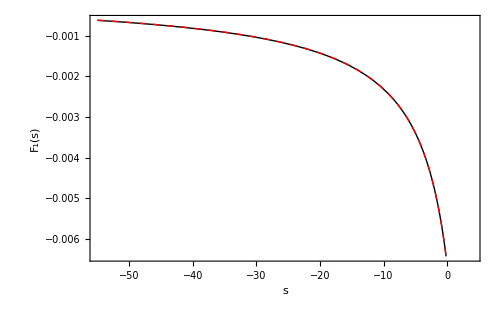

```mathematica
FullPlot=Plot[{ SmoothFF[s], myF1AltRep[s]/s},{s,-55,4},PlotStyle->{{Thick,Black},{Thick,Red,Dashed}},Frame->True,FrameStyle->Black,FrameLabel->{"s","F_1(s)"},RotateLabel->True,LabelStyle->{Black,18,FontFamily->"Times New Roman"},ImageSize->500]
```

#### First Order Results at different Dmax

```mathematica
ff10
```

{0.0117585,0.0107138,0.00871717,0.00594648,0.,0.,0.,0.,0.,0.,0.,0.,0.00265277,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ff12
```

{0.00991325,0.00929037,0.00808378,0.00636931,0.,0.,0.00425498,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00187705,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ff14
```

{0.00856508,0.00816459,0.00738234,0.00625492,0.00483507,0.,0.,0.,0.,0.,0.00318939,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00139736,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ff16
```

{0.007538,0.00726556,0.00673052,0.00595224,0.00495883,0.00378624,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00247699,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00108036,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ff18
```

{0.00672996,0.00653635,0.00615471,0.005596,0.00487632,0.00401636,0.,0.,0.,0.00304088,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00197808,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000860074,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ff20
```

{0.00607786,0.0059354,0.00565382,0.00523972,0.00470281,0.00405567,0.00331348,0.,0.,0.,0.,0.,0.,0.,0.,0.00249364,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00161548,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000700839,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ff22
```

{0.00554066,0.00543281,0.00521923,0.00490406,0.00449343,0.00399535,0.00341951,0.00277711,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00208069,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00134386,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000582029,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ff24
```

{0.0050905,0.00500691,0.00484111,0.00459582,0.00427507,0.00388412,0.0034294,0.00291836,0.,0.,0.,0.,0.00235942,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00176174,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00113523,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000491042,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ff26
```

{0.00470786,0.00464177,0.00451052,0.00431596,0.0040608,0.00374865,0.00338387,0.00297159,0.00251759,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00202826,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00151048,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000971555,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000419826,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ff28
```

{0.00437863,0.00432548,0.00421982,0.00406295,0.00385675,0.00360374,0.00330698,0.00297008,0.00259713,0.00219265,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00176156,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00130911,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00084082,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000363044,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ff30
```

{0.00409238,0.004049,0.0039627,0.00383439,0.00366544,0.00345763,0.00321317,0.00293466,0.00262503,0.00228758,0.,0.,0.,0.,0.,0.,0.00192588,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00154377,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00114531,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000734757,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000317044,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

#### Compute integrated form factor at positive s

```mathematica
(*Compute 2-particle mass matrix with closed-form expression; then assign a fix value to contribution from each intermediate state 1/(2(2LMaxJacobi+5)), then sum up to generate integrated form factor in positive s regime (see one-loop section for further details)*)
Clear[m,n];
Boson2ϕMassMatrix[l_,lp_]:= 2 √(((3+2 m) (1+n) (2+n) (3+2 n))/((1+m) (2+m)))/.{n->Min[l,lp],m->Max[l,lp]};
LMaxJacobi=484;
MϕϕJacobi=Outer[Boson2ϕMassMatrix[#1,#2]&,Range[0,LMaxJacobi,2],Range[0,LMaxJacobi,2]];

JacobiVals=√Eigenvalues[MϕϕJacobi//N]//Reverse;

arccoshlist=Table[2*ArcCosh[JacobiVals[[a]]/2],{a,2,Length[JacobiVals]}];
plotJacobi=Table[{%[[a]],(Accumulate[1/JacobiVals][[a]])/(2(2LMaxJacobi+5))},{a,Length[%]}];
```

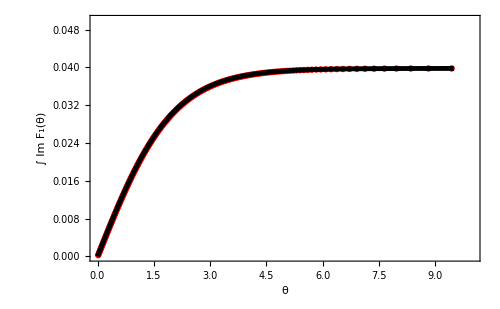

```mathematica
Show[ListPlot[plotJacobi,PlotRange->{{0,10},{0,0.05}},PlotStyle->Red],Plot[NIntegrate[1/π Im[-myF1AltRep[s]/s],{s,4,sp}/.sp->4 Cosh[θ/2]^2],{θ,0,9.5},PlotStyle->{Black,Thickness[0.007]}],Frame->True,FrameStyle->Black,FrameLabel->{"θ","∫ Im F_1(θ)"},RotateLabel->True,LabelStyle->{Black,18,FontFamily->"Times New Roman"},ImageSize->500]
```

### Generating two-loop result

```mathematica
(*Generate odd and even sectors of the mass term (unperturbed Hamiltonian) and the interaction term*)
massodd=massFuncOdd[Dmax];
intodd=intFuncOdd[Dmax];
masseven=massFuncEven[Dmax];
inteven=intFuncEven[Dmax];
(*Extract eigenvectors and eigenvalues; define the ground state to be that only containing the one-particle state*)
{valsEven,vecsEven}=masseven//N//Eigensystem//Transpose//Sort//Transpose;
{valsOdd,vecsOdd}=massodd//N//Eigensystem//Transpose//Sort//Transpose;
valsEven=Sqrt[valsEven];
valsOdd=Sqrt[valsOdd];

minstate=Table[0,StateDimsOdd[Dmax,nmax]//Length];
minstate[[1]]=1;
```

```mathematica
(*This is trying to compute the first order perturbation to even eigenvalues, even eigenvectors, and the ground state.*)
EInverses=Outer[If[#1==#2,0,1/(#1^2-#2^2)]&,valsEven,valsEven];
intvecs=vecsEven.inteven.Transpose[vecsEven];
OFPTMat=EInverses*intvecs;
vecsEven1=OFPTMat.vecsEven;
valsEven1sq=Diagonal[intvecs];

minstate1=Sum[(vecsOdd[[n]].intodd.minstate)/(1-valsOdd[[n]]^2)*vecsOdd[[n]],{n,2,valsOdd//Length}];
```

```mathematica
(*This is the list of values of q with the on-shell condition applied.*)
q1list=Table[-2/(x^2+√(-2+x) x √(2+x))/.x->valsEven[[n]],{n,1,valsEven//Length}];
q2list=-1-q1list;
```

```mathematica
(*Construct the oppropriate ϕ and ϕ^3 contributions to the second order form factor*)
phiSOqpart[q_]=minstate.phi[q].Transpose[vecsEven];
phi3SO1qpart[q_]=minstate.phi3[q].Transpose[vecsEven];
phi3SO2qpart[q_]=minstate.phi3[q].Transpose[vecsEven1];
phi3SO3qpart[q_]=minstate1.phi3[q].Transpose[vecsEven];
```

```mathematica
(*Multiply by the factor <T_(--)|μ> and apply the correct q value*)
l=q1list//Length;
phiSOlist1=vecsEven[[;;,1]]*(ReplaceAll[phiSOqpart[q][[#]],q->q1list[[#]]]&/@Range[l]);
phi3SO1list1=vecsEven1[[;;,1]]*(ReplaceAll[phi3SO1qpart[q][[#]],q->q1list[[#]]]&/@Range[l]);
phi3SO2list1=vecsEven[[;;,1]]*(ReplaceAll[phi3SO2qpart[q][[#]],q->q1list[[#]]]&/@Range[l]);
phi3SO3list1=vecsEven[[;;,1]]*(ReplaceAll[phi3SO3qpart[q][[#]],q->q1list[[#]]]&/@Range[l]);
```

```mathematica
phiSOlist2=vecsEven[[;;,1]]*(ReplaceAll[phiSOqpart[q][[#]],q->q2list[[#]]]&/@Range[q2list//Length]);
phi3SO1list2=vecsEven1[[;;,1]]*(ReplaceAll[phi3SO1qpart[q][[#]],q->q2list[[#]]]&/@Range[q2list//Length]);
phi3SO2list2=vecsEven[[;;,1]]*(ReplaceAll[phi3SO2qpart[q][[#]],q->q2list[[#]]]&/@Range[q2list//Length]);
phi3SO3list2=vecsEven[[;;,1]]*(ReplaceAll[phi3SO3qpart[q][[#]],q->q2list[[#]]]&/@Range[q2list//Length]);
```

```mathematica
phiSO=phiSOlist1+phiSOlist2;
phi3SO=phi3SO1list1+phi3SO2list1+phi3SO3list1+phi3SO1list2+phi3SO2list2+phi3SO3list2;
```

```mathematica
(*Construct the full form factor and extract Taylor expansion coefficients*)
formfactorSO=1/(2Sqrt[12π])(3/2*1/24^2*1/2 phiSO+1/6 phi3SO);
SmoothFFSO[s_]=Sum[formfactorSO[[a]]/(s-valsEven[[a]]^2)+(10valsEven1sq[[a]])/((s-valsEven[[a]]^2)^2)ff[[a]],{a,valsEven//Length}];
taylorCoef=CoefficientList[Series[SmoothFFSO[s],{s,0,8}]//Normal,s]
```

{0.00115496,0.00050288,0.000164665,0.0000490672,0.000013951,3.85365×10^-6,1.04305×10^-6,2.77968×10^-7,7.31604×10^-8}

```mathematica
(*Construct the ϕ and ϕ^3 contributions to the form factor and extract Taylor expansion coefficients*)
SmoothFFSOPhiOnly[s_]=(1/(2Sqrt[12π])(3/2*1/24^2*1/2 phiSO))/(s-valsEven^2)//Total;
SmoothFFSOPhi3Only[s_]=(1/(2Sqrt[12π])(1/6 phi3SO))/(s-valsEven^2)+(10valsEven1sq)/((s-valsEven^2)^2)ff//Total;
taylorCoefPhi=CoefficientList[Series[SmoothFFSOPhiOnly[s],{s,0,8}]//Normal,s]
taylorCoefPhi3=CoefficientList[Series[SmoothFFSOPhi3Only[s],{s,0,8}]//Normal,s]
```

{-0.00053267,-0.0000995394,-0.0000207359,-4.53484×10^-6,-1.02035×10^-6,-2.33727×10^-7,-5.4144×10^-8,-1.26301×10^-8,-2.95874×10^-9}

{0.00168763,0.00060242,0.000185401,0.0000536021,0.0000149714,4.08738×10^-6,1.0972×10^-6,2.90598×10^-7,7.61191×10^-8}

#### Taylor Coefficient Results

```mathematica
(*Taylor coefficient list of form factors at different Δmax*)
taylorCoef10={0.0005213674034212503,0.00016591271044318377,0.00004525338206728037,0.000011861327818502369,3.0572387728052045*^-6,7.810722269772197*^-7,1.984981392952474*^-7,5.0271769092297896*^-8,1.2701463802354958*^-8};
taylorCoef12={0.0005454687041410789,0.00016971631945305026,0.00004590232377430204,0.000011982428679978842,3.0816358310901285*^-6,7.862966221497476*^-7,1.9966997803997055*^-7,5.0543480673275804*^-8,1.2765909382232178*^-8};
taylorCoef14={0.0005669901060436529,0.0001731827431514071,0.000046540324407834964,0.000012111848238795508,3.1094675809188615*^-6,7.924911485640358*^-7,2.0107764103472855*^-7,5.0867624142281916*^-8,1.2841232649729794*^-8};
taylorCoef16={0.0005837569400764006,0.00017571356072800787,0.00004698817653896237,0.000012199568549238476,3.127668777650191*^-6,7.964016839477658*^-7,2.0193764137582776*^-7,5.1060026484771716*^-8,1.2884864638355666*^-8};
taylorCoef18={0.0005969778626864807,0.00017760719561134782,0.000047315134621428985,0.000012262693537274868,3.14065061580886*^-6,7.991788380107226*^-7,2.025481220091576*^-7,5.119693946447042*^-8,1.2916045629596513*^-8};
taylorCoef20={0.0006084205294196257,0.00017925843186615738,0.000047608074052213935,0.000012320787405198485,3.152880574549889*^-6,8.018480253198053*^-7,2.0314481739339085*^-7,5.133262162235059*^-8,1.294729095109742*^-8};
taylorCoef22={0.0006180154129596524,0.00018060751948316436,0.00004784436039139701,0.000012367070031351996,3.1624977784397067*^-6,8.039194472173841*^-7,2.0360191867815392*^-7,5.1435273736863416*^-8,1.297065241725894*^-8};
taylorCoef24={0.0006261140997293228,0.0001817160171050099,0.00004803605131455482,0.000012404265683951502,3.17017035144324*^-6,8.055631489792345*^-7,2.0396330132670724*^-7,5.1516245066344595*^-8,1.2989058217028115*^-8}
taylorCoef26={0.0006332885529787488,0.00018270000337935625,0.000048208463538159425,0.000012438161790159774,3.177248235555882*^-6,8.070966627129525*^-7,2.043039395700251*^-7,5.1593274386618917*^-8,1.3006711282435146*^-8};
taylorCoef28={0.0006395797706647305,0.00018354779602910445,0.00004835593273779168,0.000012466970362673271,3.18322574456802*^-6,8.083835283108449*^-7,2.0458796744331096*^-7,5.165709568882116*^-8,1.302124663638623*^-8};
taylorCoef30={0.0006451226969808421,0.0001842783546269769,0.000048481667873662637,0.00001249133590083547,3.188247170094317*^-6,8.094582820618816*^-7,2.0482398637500537*^-7,5.170989776207527*^-8,1.3033226659484298*^-8};
taylorCoef32={0.0006502477911254018,0.0001849579046374582,0.00004859987404808431,0.000012514416710211338,3.1930271279827467*^-6,8.104843370604221*^-7,2.0504965725050798*^-7,5.176041850867969*^-8,1.3044691903137673*^-8};
```

{0.000626114,0.000181716,0.0000480361,0.0000124043,3.17017×10^-6,8.05563×10^-7,2.03963×10^-7,5.15162×10^-8,1.29891×10^-8}

```mathematica
(*Taylor coefficient list of ϕ contributions to the form factor at different Δmax, same values of Δmax as above but just put them together*)
CoefListPhi={{-0.0008566337719298244,-0.00016045307492803208,-0.0000334236527111938,-7.310955883200112*^-6,-1.6449085069572229*^-6,-3.7694977724668107*^-7,-8.750485628616415*^-8,-2.0508716836178595*^-8,-4.8422948358734055*^-9},{-0.0010190217391304345,-0.00019093471509586818,-0.00003977434416772595,-8.70024765611881*^-6,-1.957507362804929*^-6,-4.4858833887123414*^-7,-1.041354374424714*^-7,-2.4406546640961434*^-8,-5.762621361687188*^-9},{-0.0011815200617284023,-0.00022142561156835984,-0.000046126988561268826,-0.000010089942179338999,-2.270194976228556*^-6,-5.202468681096843*^-7,-1.2077060541369125*^-7,-2.8305440507883366*^-8,-6.683198273489281*^-9},{-0.0013440860215053795,-0.0002519226858995066,-0.00005248087860112562,-0.000011479895738065946,-2.5829394522625364*^-6,-5.919182040283821*^-7,-1.3740871111097396*^-7,-3.220501669700494*^-8,-7.60393518567969*^-9},{-0.0015066964285713794,-0.00028242404916510827,-0.00005883561334567033,-0.000012870025402314884,-2.8957225370652105*^-6,-6.635982351570231*^-7,-1.540488108221221*^-7,-3.61050559920226*^-8,-8.52478067571412*^-9},{-0.0016693376068377009,-0.0003129284980246706,-0.00006519094752576381,-0.000014260280136613189,-3.208533025461424*^-6,-7.352844370443328*^-7,-1.7069032542390602*^-7,-4.000542386495236*^-8,-9.445703197220946*^-9},{-0.0018320009689927533,-0.00034343523553723794,-0.00007154672247647098,-0.000015650626853079204,-3.5213636606693794*^-6,-8.069751750048862*^-7,-1.8733287999703482*^-7,-4.390603323296431*^-8,-1.0366682331772308*^-8},{-0.001994680851064824,-0.00037394371510510356,-0.00007790283097348916,-0.00001704104317313741,-3.83420953756013*^-6,-8.786693442790702*^-7,-2.0397622119931104*^-7,-4.7806825257493225*^-8,-1.12877042844081*^-8},{-0.0021573733660140834,-0.0004044535502111642,-0.00008425919794408554,-0.00001843151342469888,-4.147067222287399*^-6,-9.503661715910431*^-7,-2.2062017172304454*^-7,-5.170775876192764*^-8,-1.220875940161508*^-8},{-0.0023200757576035762,-0.00043496446021755675,-0.00009061576925977324,-0.00001982202630795777,-4.459934239661263*^-6,-1.0220650996151611*^-6,-2.372646037873462*^-7,-5.5608804073095445*^-8,-1.3129840727060608*^-8},{-0.0024827860168621144,-0.0004654762365802186,-0.00009697250489991382,-0.00002121257346880564,-4.772808760072229*^-6,-1.0937657164245934*^-6,-2.539094229534677*^-7,-5.9509939261502826*^-8,-1.4050943119961555*^-8},{-0.002645502645882048,-0.0004959887214231754,-0.00010332937469162827,-0.00002260314861082116,-5.085689404942549*^-6,-1.1654677116898638*^-6,-2.705545580823187*^-7,-6.341114780912027*^-8,-1.497206270826144*^-8}};
```

```mathematica
(*Taylor coefficient list of ϕ^3 contributions to the form factor at different Δmax, same values of Δmax as above but just put them together*)
CoefListPhi3={{0.0013780011753510746,0.0003263657853712158,0.00007867703477847416,0.000019172283701702476,4.7021472797624266*^-6,1.1580220042239006*^-6,2.860029955814115*^-7,7.078048592847648*^-8,1.7543758638228364*^-8},{0.0015644904432715132,0.0003606510345489184,0.00008567666794202799,0.00002068267633609765,5.039143193895057*^-6,1.2348849610209816*^-6,3.038054154824419*^-7,7.495002731423722*^-8,1.852853074391936*^-8},{0.0017485101677720554,0.000394608354719767,0.0000926673129691038,0.00002220179041813451,5.3796625571474176*^-6,1.3127380166737203*^-6,3.218482464484198*^-7,7.917306465016528*^-8,1.952443092321908*^-8},{0.00192784296158178,0.0004276362466275145,0.00009946905514008798,0.00002367946428730442,5.710608229912727*^-6,1.388319887976148*^-6,3.393463524868017*^-7,8.326504318177665*^-8,2.0488799824035355*^-8},{0.0021036742912578605,0.0004600312447764561,0.00010615074796709933,0.000025132718939589755,6.036373152874071*^-6,1.462777073167746*^-6,3.565969328312797*^-7,8.730199545649302*^-8,2.144082630531063*^-8},{0.002277758136257327,0.000492186929890828,0.00011279902157797774,0.000026581067541811677,6.361413600011313*^-6,1.537132462364138*^-6,3.738351428172969*^-7,9.133804548730295*^-8,2.239299414831837*^-8},{0.002450016381952406,0.0005240427550204023,0.00011939108286786797,0.000028017696884431197,6.683861439109087*^-6,1.6108946222222702*^-6,3.9093479867518876*^-7,9.534130696982773*^-8,2.3337334749031248*^-8},{0.002620794950794147,0.0005556597322101134,0.00012593888228804397,0.00002944530885708891,7.00437988900337*^-6,1.6842324932583047*^-6,4.0793952252601826*^-7,9.932307032383782*^-8,2.4276762501436215*^-8},{0.0027906619189928326,0.0005871535535905204,0.000132467661482245,0.000030869675214858654,7.3243154578432806*^-6,1.7574628343039957*^-6,4.2492411129306965*^-7,1.0330103314854657*^-7,2.5215470684050228*^-8},{0.002959655528268307,0.0006185122562466612,0.00013897170199756494,0.000032288996670631036,7.643159984229284*^-6,1.8304486279260063*^-6,4.418525712306572*^-7,1.0726589976191662*^-7,2.6151087363446838*^-8},{0.003127908713842956,0.0006497545912071954,0.00014545417277357642,0.000033703909369641105,7.961055930166545*^-6,1.903223998486475*^-6,4.587334093284731*^-7,1.1121983702357809*^-7,2.708416977944585*^-8},{0.0032957504370074494,0.0006809466260606335,0.00015192924873971256,0.000035117565321032495,8.278716532925297*^-6,1.975952048750286*^-6,4.7560421533282676*^-7,1.1517156631779997*^-7,2.8016754611399108*^-8}};
```

#### Produce Taylor Coefficient Plots

```mathematica
CoefList = {taylorCoef10,taylorCoef12,taylorCoef14,taylorCoef16,taylorCoef18,taylorCoef20,taylorCoef22,taylorCoef24,taylorCoef26,taylorCoef28,taylorCoef30,taylorCoef32};
```

```mathematica
(*Get Taylor coefficients for two-loop result from Feynman diagram*)
realCoef=CoefficientList[Series[myF2[s]/s,{s,0,8}]//Normal,s];
```

```mathematica
dmaxlist={10,12,14,16,18,20,22,24,26,28,30,32};
```

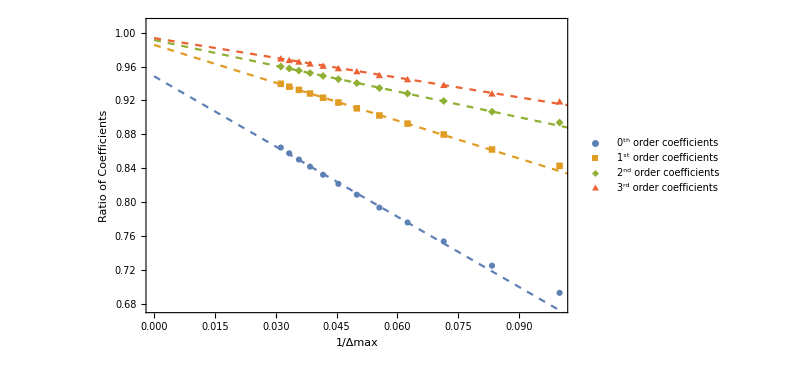

{0.948594,0.985574,0.991323,0.993597,0.994842,0.995628,0.996172,0.996575,0.99689}

```mathematica
TaylorCoeffsPlot=ListPlot[{Thread[{1/dmaxlist,CoefList[[;;,1]]/realCoef[[1]]}],Thread[{1/dmaxlist,CoefList[[;;,2]]/realCoef[[2]]}],Thread[{1/dmaxlist,CoefList[[;;,3]]/realCoef[[3]]}],Thread[{1/dmaxlist,CoefList[[;;,4]]/realCoef[[4]]}]},PlotLegends->{"0^th order coefficients","1^st order coefficients","2^nd order coefficients","3^rd order coefficients"},PlotRange->{{0,Automatic},{Automatic,1.01}},PlotMarkers->Automatic];
Do[myfit[nTaylor]=FindFit[Thread[{1/dmaxlist,CoefList[[;;,nTaylor+1]]/realCoef[[nTaylor+1]]}][[3;;-1]],a+b x,{a,b},x],
{nTaylor,0,8}];
TaylorCoeffsFitPlot=Plot[a +b x/.(myfit/@Range[0,3])//Evaluate,{x,0,0.11},PlotStyle->Dashed];
Show[TaylorCoeffsPlot,TaylorCoeffsFitPlot,Frame->True,FrameLabel->{"1/Δmax","Ratio of Coefficients"},BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->600,RotateLabel->True]
Table[a/.myfit[nTaylor],{nTaylor,0,8}]
```

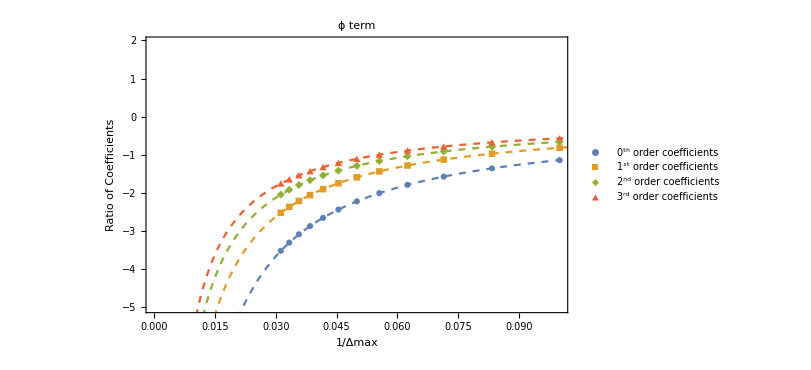

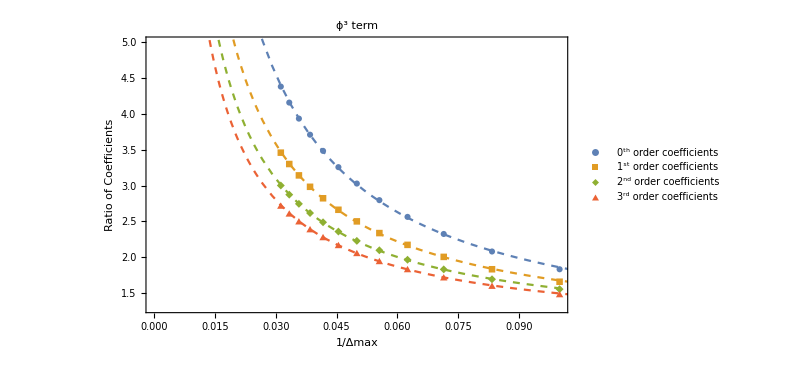

```mathematica
TaylorCoeffsPhiPlot=ListPlot[{Thread[{1/dmaxlist,CoefListPhi[[;;,1]]/realCoef[[1]]}],Thread[{1/dmaxlist,CoefListPhi[[;;,2]]/realCoef[[2]]}],Thread[{1/dmaxlist,CoefListPhi[[;;,3]]/realCoef[[3]]}],Thread[{1/dmaxlist,CoefListPhi[[;;,4]]/realCoef[[4]]}]},PlotLegends->{"0^th order coefficients","1^st order coefficients","2^nd order coefficients","3^rd order coefficients"},PlotRange->{{0,Automatic},{Automatic,-5}},PlotMarkers->Automatic];
TaylorCoeffsPhi3Plot=ListPlot[{Thread[{1/dmaxlist,CoefListPhi3[[;;,1]]/realCoef[[1]]}],Thread[{1/dmaxlist,CoefListPhi3[[;;,2]]/realCoef[[2]]}],Thread[{1/dmaxlist,CoefListPhi3[[;;,3]]/realCoef[[3]]}],Thread[{1/dmaxlist,CoefListPhi3[[;;,4]]/realCoef[[4]]}]},PlotLegends->{"0^th order coefficients","1^st order coefficients","2^nd order coefficients","3^rd order coefficients"},PlotRange->{{0,Automatic},{Automatic,5}},PlotMarkers->Automatic];
Do[myfitphi[nTaylor]=FindFit[Thread[{1/dmaxlist,CoefListPhi[[;;,nTaylor+1]]/realCoef[[nTaylor+1]]}],a1+b1/x,{a1,b1},x],
{nTaylor,0,5}]
Do[myfitphi3[nTaylor]=FindFit[Thread[{1/dmaxlist,CoefListPhi3[[;;,nTaylor+1]]/realCoef[[nTaylor+1]]}],a2+b2/x,{a2,b2},x],
{nTaylor,0,5}]
TaylorCoeffsFitPhiPlot=Plot[a1 +b1/x/.(myfitphi/@Range[0,3])//Evaluate,{x,0,0.11},PlotStyle->Dashed];
TaylorCoeffsFitPhi3Plot=Plot[a2 +b2/x/.(myfitphi3/@Range[0,3])//Evaluate,{x,0,0.11},PlotStyle->Dashed];
Show[{TaylorCoeffsPhiPlot,TaylorCoeffsFitPhiPlot},Frame->True,FrameLabel->{"1/Δmax","Ratio of Coefficients"},AxesOrigin->{0,2},BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->600,RotateLabel->True,PlotLabel->"ϕ term"]
Show[{TaylorCoeffsPhi3Plot,TaylorCoeffsFitPhi3Plot},Frame->True,FrameLabel->{"1/Δmax","Ratio of Coefficients"},BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->600,RotateLabel->True,PlotLabel->"ϕ^3 term"]
```